# TranscendentalRange

Generate ranges of transcendental numbers

## Definition

### Auxiliary functions

#### FormulaComplexity

```mathematica
ClearAll[formulaComplexity]

digitSum[int_Integer]:=If[$VersionNumber>=14,DigitSum[int],Total@IntegerDigits[int]]

formulaComplexity[form_?NumericQ]:=
	N@Total[Cases[
			Inactivate[form]
		/.const_?(Quiet@MemberQ[Attributes[#],Constant]&):>1
			/.c_Complex:>ReIm[c]
				/.r:Rational[i1_Integer,i2_Integer]:>{i1,i2}
					/.Inactive[Sqrt][arg_]:>Inactive[Sqrt[{arg,arg}]]
						/.Alternatives[
							Inactive[Power][b_,Inactive[Times][m_,Inactive[Power][n_,-1]]|{m_,n_}],
							Inactive[Power][{b_},Inactive[Times][m_,Inactive[Power][n_,-1]]|{m_,n_}]]:>
								Table[b,Abs[n]+Abs[m]],
			_Integer,{0,Infinity}]/. j_Integer?NonPositive:>-j+1
				/.i_Integer:>Mean[1/2{5IntegerLength[i],digitSum[i],Total[Last/@FactorInteger[i]],Sqrt[Abs[N[i]]]}]]
```

#### Restricted range

```mathematica
complexitySelect[list_List,c_]:=
	Select[list,formulaComplexity[#]<=c&]

ClearAll[stepSelect]
stepSelect[list_List,d_]:=
	Block[{sel,eln,i},
	eln=list[[1]];
	sel=CreateDataStructure["DynamicArray"];
	sel["Append",eln];

	For[i=2,i<=Length[list],i++,

		If[Abs[list[[i]]-eln]>=d,

			eln=list[[i]];
			sel["Append",eln],

			Continue[]]];

	Normal@sel]~Quiet~N::meprec

stepSelect[{},d_]:=
	{}

stepSelect[{},d_,t_:0]:=
	{}
```

```mathematica
restrictRange[main_,compl_,d_:0]:=
	If[d!=0,stepSelect[#,d],#]&[complexitySelect[main,compl]]
```

### Generator ranges

#### AlgebraicRange

```mathematica
ClearAll[algebraicRange]
algebraicRange[args__]:=ResourceFunction["AlgebraicRange"][args];
```

#### FareyRange

```mathematica
ClearAll[fareyRange]
fareyRange[r1_,r2_,r3_]:=
	If[r3>=1,
		ResourceFunction["FareyRange"][r1,r2,r3],
		Which[(*intuitive alternative reciprocal step*)
			MatchQ[r3,Rational[1,_]],
				ResourceFunction["FareyRange"][r1,r2,1/r3],
			MatchQ[r3,Rational[-1,_]],
				Reverse[ResourceFunction["FareyRange"][r2,r1,-1/r3]],
			True,
				failureFareyStep[r3]]]
```

#### Basic range

```mathematica
range[x_,y_,z_,opt_String]:=
Switch[opt,
		"Rational",
			Range[x,y,z],
		"Algebraic",
			algebraicRange[x,y,z],
		"RationalFarey",
			fareyRange[x,y,z],
		"AlgebraicFarey",
			algebraicRange[x,y,z,"FareyRange"->True]]
```

#### Argument failures

```mathematica
failureNotAlgebraics=
Failure["ArgsNotAlgebraic",<|"MessageTemplate"->"The range arguments provided `ls` are not all algebraic numbers.","MessageParameters"-><|"ls"->#|>|>]&;
```

```mathematica
failureFareyStep=Failure["FareyStep",<|"MessageTemplate"->"The step parameter `s` is not allowed with the Farey range option.","MessageParameters"-><|"s"->#|>|>]&;
```

### Method features

#### Transcendental types

All possible methods include the following transcendental functions types:

```mathematica
$trig={Sin,Cos,Tan,Cot,Sec,Csc};
$hyp={Sinh,Cosh,Tanh,Coth,Sech,Csch};
$invtrig={ArcSin,ArcCos,ArcTan,ArcCot,ArcSec,ArcCsc};
$invhyp={ArcSinh,ArcCosh,ArcTanh,ArcCoth,ArcSech,ArcCsch};
$trsctypes=Join[{Exp,Log,Power},$trig,$hyp,$invtrig,$invhyp];
```

#### Domains

Domains for the transcendental functions (namely, for the second arguments of Outer or monotonicOuter):

```mathematica
ClearAll[domain]
domain[_]=True&;
domain[Log]=#>0&;
domain[Power]=#>0&;
domain[Coth]=#!=0&;
domain[Csch]=#!=0&;
domain[ArcCosh]=#>=1&;
domain[ArcTanh]=-1<#<1&;
domain[ArcCoth]=Abs[#]>1&;
domain[ArcSech]=0<#<=1&;
domain[ArcCsch]=#!=0&;
domain[Tan]=Abs@FractionalPart[#/π]!=1/2&;
domain[Sec]=Abs@FractionalPart[#/π]!=1/2&;
domain[Cot]=FractionalPart[#/π]!=0&;
domain[Csc]=FractionalPart[#/π]!=0&;
domain[ArcSin]=Abs[#]<=1&;
domain[ArcCos]=Abs[#]<=1&;
domain[ArcCot]=#!=0&;
domain[ArcSec]=Abs[#]>=1&;
domain[ArcCsc]=Abs[#]>=1&;
```

#### Turning points

```mathematica
turning[Sech,2]=1.1996786402577338339163698486411419442614587884186072089154777839181247252238474799990869921465093798859055084152992885360972178040896927668397975864210455901058557964724175753128553208906269191698657332448131052287075914748630366427440133082155799942721734256655069966143444470563164230057692043247489031265201307085790014912003399776696436986439748912548615777187811288374137950992076841745184393198667506764368371596365491614153402516039184082319627130193295329591196622738714420280530632359907736850113404270016907041313721058255097372805899876759275956586915101399092579666079294066380624790347342258402538842785309098110628017951680269086797741369710360546711669340271234106682950933277105045783881899238434275271058676877566415006355465162567059563426708149738219386927460413758456500330564478415290540016678779191401214582555423223492792011045769305102525934838833146509338813489679566942703705429701575293800309363707379469515406928261504019581432610649384677565523318326483365941764424827272107434379332462505643`1000.(*Entity["MathematicalConstant","CothFixedPointConstant"][EntityProperty["MathematicalConstant","NumericalApproximation"]]*);

rooteq[ArcSech,2]=D[x ArcSech[x],x]==0//PowerExpand//Simplify;
turning[ArcSech,2]=With[{prec=1000},FindRoot[rooteq[ArcSech,2],{x,0.5},PrecisionGoal->prec,WorkingPrecision->prec][[1,2]]];

rooteq[ArcCos,2]=D[x ArcCos[x],x]==0//PowerExpand//Simplify;
turning[ArcCos,2]=With[{prec=1000},FindRoot[rooteq[ArcCos,2],{x,0.5},PrecisionGoal->prec,WorkingPrecision->prec][[1,2]]];

rooteq[ArcSec,2]=D[ x ArcSec[x],x]==0//PowerExpand//Simplify;
turning[ArcSec,2]=With[{prec=1000},FindRoot[rooteq[ArcSec,2],{x,-10},PrecisionGoal->prec,WorkingPrecision->prec][[1,2]]];

rooteq[Power,2]=D[ (-x)^x,x]==0//Simplify;
turning[Power,2]=With[{prec=1000},FindRoot[rooteq[Power,2],{x,-0.1},PrecisionGoal->prec,WorkingPrecision->prec][[1,2]]];
```

### Method implementations

#### General testing method

The following general method is simpler to implement but also "naive" in the sense that it uses the default inefficient version of Outer. Then it can be used as a method for testing the more sophisticated efficient implementation with monotonicOuter.

(It is also currently the default method for direct trigonometric functions.)

```mathematica
(*elementary testing range with only one function at a time*)

ClearAll[elemNaiveRange]

elemNaiveRange[x_,y_,z_,{fun:_Symbol|_String:Exp,1},opt_String:"Rational"]/;NumericQ[z]:=
Block[
{rgmain,min=If[x<y,x,y],max=If[x<y,y,x]},

(*arguments basic range, to be restricted below*)
rgmain=range[x,y,z,opt];

DeleteCases[
Select[

Outer[

(*function with two arguments*)
Which[
MemberQ[{Exp,Log,Splice@Join[$trig,$hyp,$invtrig,$invhyp]},fun],
	#1 fun[#2],
fun===Power,
	#2^#1,
True,
	$Failed]&,

(*first argument*)
Which[
	MemberQ[{Exp,Log,Splice@Join[$trig,$hyp,$invtrig,$invhyp]},fun],
		rgmain,
	fun===Power,
			DeleteCases[rgmain,_Rationals]],

(*second argument*)
Which[

		MemberQ[{Log,Power,Coth,Csch,ArcCosh,ArcTanh,ArcCoth,ArcSech,ArcCsch,Tan,Sec,Cot,Csc,ArcSin,ArcCos,ArcCot,ArcSec,ArcCsc},fun],
			Select[rgmain,domain[fun]],

		True,
			rgmain
		]]//Flatten,
min<=#<=max&],
_?(Element[#,Algebraics]&)]]
```

```mathematica
elemNaiveRange[x_,y_,z_,{fun:_Symbol|_String:Exp,m_Integer},opt_String:"Rational",prec_:MachinePrecision]/;m>1&&NumericQ[z]:=Block[{base,combined,op,min=If[x<y,x,y],max=If[x<y,y,x],rpl},rpl=If[fun=!=Power,Times[a_,fun[arg_]]|fun[arg_]:>Abs@N[arg,prec],Power[b_,e_]:>Abs@N[b,prec]+Abs@N[e,prec]];
base=Values@Map[First@MinimalBy[#,#/.rpl&,1]&,GroupBy[elemNaiveRange[x,y,z,{fun,1},opt],N[#,prec]&]];
op=If[fun===Power,Times,Plus];
combined=base;
Do[combined=Values@Map[First@MinimalBy[#,#/.rpl&,1]&,GroupBy[Select[Union@Flatten@Outer[op,combined,base],min<=#<=max&],N[#,prec]&]],{m-1}];
DeleteCases[combined,_?(Element[#,Algebraics]||Abs@N[#,prec]<10^(-prec+1)&)]]
```

```mathematica
ClearAll[combinedNaiveRange];

Options[combinedNaiveRange]={WorkingPrecision->MachinePrecision,"GeneratorsDomain"->Rationals,"Multiplicity"->1};

combinedNaiveRange[x_,y_,z_:1,funs_List,opts:OptionsPattern[combinedNaiveRange]]/;NumericQ[z]:=
	Block[{funL,patf,extrarg,join,
		prec=OptionValue[WorkingPrecision],
		m=OptionValue["Multiplicity"],
		optalg=optGenerators[OptionValue["GeneratorsDomain"]]},
		funL=If[funs=!={All},
			Flatten@funs,
			$trsctypes];

		patf=_?(MemberQ[$trsctypes,#]&);
		extrarg=#/.Times[a_, patf[arg_]]|patf[arg_]:>Abs@N[arg,prec]&;

		join=If[MemberQ[{1,{1}},m],
			Join@@Map[elemNaiveRange[x,y,z,{#,m},optalg]&,funL],
			Flatten[Join@@@Map[elemNaiveRange[x,y,z,{#,m},optalg]&,{
						Cases[funL,Alternatives@@Join[{Exp},$trig,$hyp]],
						Cases[funL,Alternatives@@Join[{Log},$invtrig,$invhyp]],
						Cases[funL,Power]},{2}],1]];

		Values@Map[First@SortBy[#,extrarg]&,GroupBy[join,N[#,prec]&]]]
```

```mathematica
sortNaiveRange[x_,y_,z_:1,fun:_Symbol|_String|_List|All,opts:OptionsPattern[combinedNaiveRange]]/;NumericQ[z]:=
	If[z>0,SortBy,ReverseSortBy][combinedNaiveRange[x,y,z,{fun},opts],N[#,OptionValue[WorkingPrecision]]&]
```

#### Monotonic outer

```mathematica
monotonicOuter[fun_Function,{min_,max_},ls1_List,ls2_List,{mi_,mj_},sign_]:=
	Block[{i,j,new,begin,end,rgQ,outer},

		outer=CreateDataStructure["DynamicArray"];

		For[
			Switch[mi,
					1,i=1,
					-1,i=Length[ls1]],
			Switch[mi,
					1,i<=Length[ls1],
					-1,i>=1],
			Switch[mi,
					1,i++,
					-1,i--],

			begin=True;

			end=False;

			For[

				Switch[mj,
					1,j=1,
					-1,j=Length[ls2]],
				Switch[mj,
					1,j<=Length[ls2],
					-1,j>=1],
				Switch[mj,
					1,j++,
					-1,j--],



				new=fun[ls1[[i]],ls2[[j]]];

				rgQ=min<=new<=max;

				If[rgQ,
					begin=False];

				Which[new>max&&sign===1,
						end=True,
					new<min&&sign===-1,
						end=True];

				Which[
					rgQ&&!begin,
						outer["Append",new],
					begin&&!end,
						(*this should be avoided with better splitting*)
						Echo[{"redundant",ls1[[i]],ls2[[j]]}];
						Continue[],
					True,
						Break[]]]];

		Normal@outer]//QuietEcho
```

#### Range preprocessing

```mathematica
(*splitRange:split a sorted list into segments at given points*)
ClearAll[splitRange]
splitRange[list_List,splitPts_List,z_,segs_,count_Symbol]:=Block[{pts,bounds,n,seg},pts=Sort[splitPts];
bounds=Join[{-Infinity},pts,{Infinity}];
n=Length[bounds]-1;
count=n;
Do[seg=Select[list,bounds[[k]]<=#<=bounds[[k+1]]&];
segs[k]=If[z>0,seg,Reverse[seg]],{k,n}];]
(*assignment to symbolic argument is OK*)
```

```mathematica
(*preprRange:prepare coefficient and argument ranges for monotonicOuter.
#1 (coefficient) takes values in the whole range[x,y,z].
#2 (argument to f) takes values only where f is defined.
Each range is split independently at its own critical points for efficient Break[] in monotonicOuter.*)
ClearAll[preprRange]

preprRange[
{x_,y_,z_,opt_},
{cAlg_,cSing_,cSplit_},
{aDom_,aAlg_,aSing_,aSplit_},
{rc_,ra_,cs_,as_,ncs_,nas_}]:=

Block[{base},

base=range[x,y,z,opt];

(*Coefficient range:full range minus algebraic/singular points*)
rc=base;
If[cAlg=!=None,rc=DeleteCases[rc,cAlg]];
If[Length[cSing]>0,rc=DeleteCases[rc,Alternatives@@cSing]];

(*Argument range:domain-restricted,minus algebraic/singular*)
ra=Select[base,aDom];
If[aAlg=!=None,ra=DeleteCases[ra,aAlg]];
If[Length[aSing]>0,ra=DeleteCases[ra,Alternatives@@aSing]];

(*no output since this merely sets block symbols*)
splitRange[rc,cSplit,z,cs,ncs];
splitRange[ra,aSplit,z,as,nas];]
```

#### Method specifications

```mathematica
(*Each entry encodes the varying parts of a coreRange definition:
  "coeff" -> {cAlg, cSing, cSplit}  -- coefficient preprocessing parameters
  "arg"   -> {aAlg, aSing, aSplit}  -- argument preprocessing parameters
  "outp"  -> {{ls1Idx, ls2Idx, {mi,mj}, sign}, ...}  -- monotonicOuter tuples for positive range
  "outn"  -> {{ls1Idx, ls2Idx, {mi,mj}, sign}, ...}  -- monotonicOuter tuples for negative range
For non-Power methods: ls1 = coefficient segments (cs), ls2 = argument segments (as).
For Power: ls1 = argument segments (as), ls2 = coefficient segments (cs) [swapped].*)

$methodSpecs=<|

Exp-><|
	"coeff"->{0,{},{0}},
	"arg"->{0,{},{-1}},
	"outp"->{{2,1,{1,-1},1},{2,2,{1,1},1}},
	"outn"->{{1,1,{-1,-1},-1},{1,2,{-1,1},-1}}|>,

Log-><|
	"coeff"->{0,{},{0}},
	"arg"->{1,{},{1/E,1}},
	"outp"->{{1,1,{-1,1},-1},{1,2,{-1,-1},1},{2,3,{1,1},1}},
	"outn"->{{2,1,{1,-1},-1},{2,2,{1,1},1},{1,3,{-1,1},-1}}|>,

Sinh-><|
	"coeff"->{0,{},{0}},
	"arg"->{0,{},{0}},
	"outp"->{{1,1,{-1,-1},1},{2,2,{1,1},1}},
	"outn"->{{2,1,{1,-1},-1},{1,2,{-1,1},-1}}|>,

Cosh-><|
	"coeff"->{0,{},{0}},
	"arg"->{0,{},{0}},
	"outp"->{{2,2,{1,1},1},{2,1,{1,-1},1}},
	"outn"->{{1,2,{-1,1},-1},{1,1,{-1,-1},-1}}|>,

Tanh-><|
	"coeff"->{0,{},{0}},
	"arg"->{0,{},{0}},
	"outp"->{{2,2,{1,1},1},{1,1,{-1,-1},1}},
	"outn"->{{1,2,{-1,1},-1},{2,1,{1,-1},-1}}|>,

Coth-><|
	"coeff"->{0,{},{0}},
	"arg"->{0,{0},{0}},
	"outp"->{{2,2,{1,-1},1},{1,1,{-1,1},1}},
	"outn"->{{1,2,{-1,-1},-1},{2,1,{1,1},-1}}|>,

Sech-><|
	"coeff"->{0,{},{0}},
	"arg"->{0,{},{-turning[Sech,2],0,turning[Sech,2]}},
	"outp"->{{2,4,{1,1},1},{2,3,{1,1},1},{2,2,{1,-1},1},{2,1,{1,-1},1}},
	"outn"->{{1,4,{-1,1},-1},{1,3,{-1,1},-1},{1,2,{-1,-1},-1},{1,1,{-1,-1},-1}}|>,

Csch-><|
	"coeff"->{0,{},{0}},
	"arg"->{0,{0},{0}},
	"outp"->{{2,2,{1,1},-1},{1,1,{-1,-1},-1}},
	"outn"->{{1,2,{-1,1},1},{2,1,{1,-1},1}}|>,

ArcSinh-><|
	"coeff"->{0,{},{0}},
	"arg"->{0,{},{0}},
	"outp"->{{1,1,{-1,-1},1},{2,2,{1,1},1}},
	"outn"->{{2,1,{1,-1},-1},{1,2,{-1,1},-1}}|>,

ArcCosh-><|
	"coeff"->{0,{},{0}},
	"arg"->{1,{},{}},
	"outp"->{{2,1,{1,1},1}},
	"outn"->{{1,1,{-1,1},-1}}|>,

ArcTanh-><|
	"coeff"->{0,{},{0}},
	"arg"->{0,{},{0}},
	"outp"->{{1,1,{-1,-1},1},{2,2,{1,1},1}},
	"outn"->{{2,1,{1,-1},-1},{1,2,{-1,1},-1}}|>,

ArcCoth-><|
	"coeff"->{0,{},{0}},
	"arg"->{0,{-1,1},{-1,1}},
	"outp"->{{2,3,{1,-1},1},{1,1,{-1,1},1}},
	"outn"->{{1,3,{-1,-1},-1},{2,1,{1,1},-1}}|>,

ArcSech-><|
	"coeff"->{0,{},{0}},
	"arg"->{1,{0},{turning[ArcSech,2]}},
	"outp"->{{2,1,{1,-1},1},{2,2,{1,-1},1}},
	"outn"->{{1,1,{-1,-1},-1},{1,2,{-1,-1},-1}}|>,

ArcCsch-><|
	"coeff"->{0,{},{0}},
	"arg"->{0,{0},{0}},
	"outp"->{{2,2,{1,-1},1},{1,1,{-1,1},1}},
	"outn"->{{1,2,{-1,-1},-1},{2,1,{1,1},-1}}|>,

ArcSin-><|
	"coeff"->{0,{},{0}},
	"arg"->{0,{},{0}},
	"outp"->{{1,1,{-1,-1},1},{2,2,{1,1},1}},
	"outn"->{{2,1,{1,-1},-1},{1,2,{-1,1},-1}}|>,

ArcCos-><|
	"coeff"->{0,{},{0}},
	"arg"->{1,{},{turning[ArcCos,2]}},
	"outp"->{{2,2,{1,-1},1},{2,1,{1,-1},1}},
	"outn"->{{1,2,{-1,-1},-1},{1,1,{-1,-1},-1}}|>,

ArcTan-><|
	"coeff"->{0,{},{0}},
	"arg"->{0,{},{0}},
	"outp"->{{1,1,{-1,-1},1},{2,2,{1,1},1}},
	"outn"->{{2,1,{1,-1},-1},{1,2,{-1,1},-1}}|>,

ArcCot-><|
	"coeff"->{0,{},{0}},
	"arg"->{0,{0},{0}},
	"outp"->{{2,2,{1,-1},1},{1,1,{-1,1},1}},
	"outn"->{{1,2,{-1,-1},-1},{2,1,{1,1},-1}}|>,

ArcSec-><|
	"coeff"->{0,{},{0}},
	"arg"->{1,{},{turning[ArcSec,2],-1,1}},
	"outp"->{{2,4,{1,1},1},{2,2,{1,1},1},{2,1,{1,1},1}},
	"outn"->{{1,4,{-1,1},-1},{1,2,{-1,1},-1},{1,1,{-1,1},-1}}|>,

ArcCsc-><|
	"coeff"->{0,{},{0}},
	"arg"->{0,{},{-1,1}},
	"outp"->{{2,3,{1,-1},1},{1,1,{-1,1},1}},
	"outn"->{{1,3,{-1,-1},-1},{2,1,{1,1},-1}}|>,

Power-><|
	"coeff"->{0,{},{turning[Power,2],0}},
	"arg"->{1,{},{1}},
	"outp"->{{1,3,{1,1},1},{2,3,{1,1},1},{1,2,{1,-1},1},{2,2,{1,-1},1},{1,1,{1,-1},1},{2,1,{1,-1},1}},
	"outn"->{}|>

|>;
```

#### Core range

```mathematica
ClearAll[computeOuter]
computeOuter[fun_Function,{min_,max_},ls1_,ls2_,tuples_List]:=
	If[tuples==={},
		{},
		Join@@(monotonicOuter[fun,{min,max},ls1[#[[1]]],ls2[#[[2]]],#[[3]],#[[4]]]&/@tuples)]
```

```mathematica
ClearAll[coreRange]

coreRange[{f_,1},x_,y_,z_:1,opt_String:"Rational"]/;KeyExistsQ[$methodSpecs,f]:=
Block[{spec=$methodSpecs[f],fun,min,max,rc,ra,cs,as,ncs,nas,
	cAlg,cSing,cSplit,aAlg,aSing,aSplit,ls1,ls2,outp,outn},

	fun=If[f===Power,#1^#2&,# f[#2]&];
	min=If[z>0,x,y];
	max=If[z>0,y,x];

	{cAlg,cSing,cSplit}=spec["coeff"];
	{aAlg,aSing,aSplit}=spec["arg"];

	preprRange[
		{x,y,z,opt},
		{cAlg,cSing,cSplit},
		{domain[f],aAlg,aSing,aSplit},
		{rc,ra,cs,as,ncs,nas}];

	(*Power: filter coefficient segments to non-rationals*)
	If[f===Power,
		Do[cs[k]=Select[cs[k],!Element[#,Rationals]&],{k,ncs}]];

	{ls1,ls2}=If[f===Power,{as,cs},{cs,as}];

	outp:=computeOuter[fun,{min,max},ls1,ls2,spec["outp"]];
	outn:=computeOuter[fun,{min,max},ls1,ls2,spec["outn"]];

	Which[
		0<=x<=y||0<=y<=x,outp,
		x<=y<=0||y<=x<=0,outn,
		x<=0&&y>=0,outn~Join~outp,
		y<=0&&x>=0,outp~Join~outn]]
```

### Main definition

#### Options

```mathematica
ClearAll[TranscendentalRange]

Options[TranscendentalRange]={Method->Exp,"GeneratorsDomain"->Rationals,"FareyRange"->False,"FormulaComplexity"->Infinity,WorkingPrecision->MachinePrecision,"Multiplicity"->1,"Test"->False(*development only option*)};
```

```mathematica
ClearAll[optGenerators]
optGenerators[opts:OptionsPattern[TranscendentalRange]]:=
	Block[{plain},
		plain=Switch[OptionValue["GeneratorsDomain"],
						Rationals|{Rationals,Reals},
							"Rational",
						Algebraics|{Algebraics,Reals},
							"Algebraic"];
		If[!OptionValue["FareyRange"],
				plain,
				plain<>"Farey"]]
optGenerators[str_String]:=str
```

#### Semifinal range

```mathematica
ClearAll[transcendentalRangeSingle]

Options[transcendentalRangeSingle]=Options[TranscendentalRange];

transcendentalRangeSingle[{f_,i_},x_,y_,z_:1,opts:OptionsPattern[transcendentalRangeSingle]]:=

Block[{prec=OptionValue[WorkingPrecision],rg,rpl,sby,ddby},

		(*raw redundant range*)
		rg=coreRange[{f,i},x,y,z,optGenerators[opts]];

		(*delete duplicates by N + choose the one with minimal argument*)
		rpl=Switch[i,
					{1,0},f[arg_]:>Abs@N[arg,prec],
					1,Times[a_, f[arg_]]|f[arg_]:>Abs@N[arg,prec]];
		ddby=Values@Map[
			First@MinimalBy[#,#/.rpl&,1]&,

			GroupBy[rg,N[#,prec]&]];

		(*(rev)sort by N*)
		sby=If[z>0,SortBy,ReverseSortBy];
		sby[ddby,N[#,prec]&]]
```

```mathematica
ClearAll[transcendentalRangeMultiple]

transcendentalRangeMultiple[fullrange_List,{method_,multi_},{x_,y_,z_},prec_:$MachinePrecision]:=DeleteCases[
If[z>0,SortBy,ReverseSortBy][DeleteDuplicatesBy[combineMultiplicity[fullrange,{method,multi},{x,y,z},prec],N[#,prec]&],N[#,prec]&],_?(Element[#,Algebraics]||Abs@N[#,prec]<10^(-prec+1)&)]
```

#### Combined ranges

```mathematica
ClearAll[combineMultiplicity]
combineMultiplicity[range_List,{f_,ord_Integer},{x_,y_,z_},prec_:$MachinePrecision]/;ord>2:=
	Block[{raw,rpl},
		raw=monotonicOuter[
			If[f=!=Power,Plus[#1,#2]&,Times[#1,#2]&],
			{Min[x,y],Max[x,y]},
			If[z>0,#,Reverse@#]&@combineMultiplicity[range,{f,ord-1},{x,y,z},prec],
			If[z>0,#,Reverse@#]&@range,
			If[z>0,{1,1},{-1,-1}],
			If[z>0,1,-1]];
		rpl=If[f=!=Power,
			Times[a_,f[arg_]]|f[arg_]:>Abs@N[arg,prec],
			Power[base_,exp_]:>Abs@N[base,prec]+Abs@N[exp,prec]];
		Values@Map[First@MinimalBy[#,#/.rpl&,1]&,GroupBy[raw,N[#,prec]&]]]
combineMultiplicity[range_List,{f_,2},{x_,y_,z_},prec_:$MachinePrecision]:=
	Block[{raw,rpl},
		raw=monotonicOuter[
			If[f=!=Power,Plus[#1,#2]&,Times[#1,#2]&],
			{Min[x,y],Max[x,y]},
			If[z>0,#,Reverse@#]&@range,
			If[z>0,#,Reverse@#]&@range,
			If[z>0,{1,1},{-1,-1}],
			If[z>0,1,-1]];
		rpl=If[f=!=Power,
			Times[a_,f[arg_]]|f[arg_]:>Abs@N[arg,prec],
			Power[base_,exp_]:>Abs@N[base,prec]+Abs@N[exp,prec]];
		Values@Map[First@MinimalBy[#,#/.rpl&,1]&,GroupBy[raw,N[#,prec]&]]]
combineMultiplicity[range_List,{f_,1},{x_,y_,z_},prec_:$MachinePrecision]:=
	range
```

```mathematica
ClearAll[combineMethod]
combineMethod[funL_List,x_,y_,z_,d_,opts:OptionsPattern[TranscendentalRange]]:=
	With[{prec=OptionValue[WorkingPrecision]},
	If[z>0,SortBy,ReverseSortBy][
	DeleteDuplicatesBy[
	Flatten[
Map[TranscendentalRange[x,y,z,d,Method->#,opts]&,
	funL],1],
		N[#,prec]&],
	N[#,prec]&]]
```

#### Final range

```mathematica
Clear[TranscendentalRange]

TranscendentalRange[x_,opts:OptionsPattern[TranscendentalRange]]:=
	TranscendentalRange[1,x,1,0,opts]

TranscendentalRange[x_,y_,z_:1,d_:0,opts:OptionsPattern[TranscendentalRange]]/;NumericQ[d]&&NumericQ[z]:=
	Block[{optmeth,optmulti,optprec,optcompl,opttest,optalg,fullrange,restrcompl,restrstep},

	If[!Element[{x,y,z},Algebraics],
			Return@failureNotAlgebraics[{x,y,z}]];

	{optmeth,optmulti,optprec,optcompl,opttest}=
	OptionValue[{Method,"Multiplicity",WorkingPrecision,"FormulaComplexity","Test"}];

	optalg=optGenerators[opts];

	fullrange=
	If[opttest||MemberQ[$trig,optmeth],


		sortNaiveRange[
			x,y,z,
			optmeth,
			"Multiplicity"->optmulti,
			"GeneratorsDomain"->optalg,
			WorkingPrecision->optprec],


		Which[

				KeyExistsQ[$methodSpecs,optmeth],
				Which[
			optmulti===1,
			#,

			IntegerQ[optmulti]&&optmulti>=2,
				transcendentalRangeMultiple[
				#,
				{optmeth,optmulti},
				{x,y,z},
				optprec],

			True,
			$Failed]&@
						transcendentalRangeSingle[
							{optmeth,1},
							x,y,z,
							opts],

				ListQ[optmeth],
			combineMethod[optmeth,x,y,z,d,opts],

				optmeth===All,
			combineMethod[$trsctypes,x,y,z,d,opts],

				True,
				$Failed]];
			

		restrcompl=If[optcompl<Infinity,
			complexitySelect[fullrange,optcompl],
			fullrange];

		restrstep=If[d>0,
			stepSelect[restrcompl,d],
			restrcompl]]
```

## Documentation

### Usage

TranscendentalRange[x]

gives all transcendental numbers of the forms t=b ⅇ^a with 1<=t<=x and a,b algebraics in Range[x].

TranscendentalRange[x,y]

gives all transcendental numbers of the forms t=b ⅇ^a, with x<=t<=y and a,b algebraics in Range[x,y].

TranscendentalRange[x,y,s]

gives all transcendental numbers of the forms t=b ⅇ^a, with x<=t<=y, s>0 and a,b algebraics in Range[x,y,s].

TranscendentalRange[x,y,s,d]

require a lower bound on the steps d.

### Details & Options

TranscendentalRange can systematically generate various types of transcendental numbers.

Transcendental numbers are irrational numbers for which it has been mathematically proven that they cannot be expressed as solutions of any polynomial equation with integer coefficients (that is, they are not Root objects at the exact level).

As for the basic function Range, the first two arguments of TranscendentalRange are the numeric bounds x, y of the range. In other words, all the range elements satisfy x<=t_i<=y.

By default, the range elements are generated according to the Lindemann-Weierstrass theorem, that is linear combinations of exponentials t_i= b ⅇ^a, for all algebraic arguments and coefficients a, b that are members of Range[x,y], or possibly Range[x,y,s] using also a step parameter s as third argument.

This transcendental range definition appears rather natural mathematically, but requires careful implementation as a customized version of Outer, so to avoid producing unnecessary expressions which will be eventually discarded since beyond the bounds.

As it happens for resource function "AlgebraicRange", also the definition of TranscendentalRange allows the user to specify a fourth argument d, to require a minimum absolute value difference between successive transcendentals and thus avoid the tendency to produce very irregular distributions of numeric values.

TranscendentalRange has been designed especially in view of its application to the resource function  "FindClosedForm" for exhaustively searching possible closed forms for raw numbers in terms of arbitrary mathematical functions with transcendental arguments.

TranscendentalRange accepts the following options:

Method | Exp | change function for generating transcendental numbers
"Multiplicity" | 1 | set the number of terms to linearly combine
"GeneratorsDomain" | Rationals | change type of algebraic arguments for the generating function
"FareyRange" | False | set the step denominators as in the FareySequence
"FormulaComplexity" | Infinity | limit the complexity of the expressions
WorkingPrecision | MachinePrecision | set the precision for all the internal numerical evaluations

The option Method can be used to specify other types of transcendental functions for generating transcendental numbers and these include:

Exp | exponential forms b ⅇ^a
Log | logarithmic forms bLog[a]
Power | power forms a^b, only for irrational b
Sin, Cos, Tan, … | any of the trigonometric forms b Sin[a],bCos[a],bTan[a], …
ArcSin, ArcCos, ArcTan, … | any of the inverse trig. forms b ArcSin[a],bArcCos[a],bArcTan[a], …
Sinh, Cosh, Tanh, … | any of the hyperbolic forms b Sinh[a],bCosh[a],bTanh[a], …
ArcSinh, ArcCosh, ArcTanh, … | any of the inverse hyp. forms bArcSinh[a],bArcCosh[a],bArcTanh[a], …
{type_1, type_2,… } | a list of the above types
All | all of the above types

For all these transcendental types, the generated exact numbers have been mathematically proven to be transcendental through the theorems of Lindemann-Weierstrass, Gelfond-Schneider and Baker (cf. Baker, 1975). They establish than any linear combination of the above types is a transcendental number.

The number of terms of such linear combinations can be specified through the option "Multiplicity", which can take the following values:

n | take linear combinations UpTo n terms

The option "GeneratorsDomain" can be used to specify whether a, b (function argument and coefficient) should belong to the Rationals or to the Algebraics, as generated by Range and the resource function "AlgebraicRange", respectively. These are also restricted to be elements of the Reals and no complex number can be generated.

For the method Power, only algebraic irrational generators in the exponent b can produce transcendental numbers. Correspondingly, the option "Multiplicity" generates product combinations.

Another way to restrict the output of TranscendentalRange is by setting a threshold for the complexity of the numeric expressions involved through the option "FormulaComplexity". The corresponding numerical values have little relevance in practice and are assigned through a merely heuristic recipe. A user interested in precise computations of the underlying homonymous function may use the paclet "DanieleGregori/GeneralizedRange".

## Examples

### Basic Examples

A range of positive transcendental numbers:

```mathematica
TranscendentalRange[10]
```

{ⅇ,2 ⅇ,ⅇ^2,3 ⅇ}

Negative and positive transcendental numbers:

```mathematica
TranscendentalRange[-2,2]
```

{-2/ⅇ,-1/ⅇ,-2/ⅇ^2,-1/ⅇ^2,1/ⅇ^2,2/ⅇ^2,1/ⅇ,2/ⅇ}

A transcendental range with non-unit step:

```mathematica
TranscendentalRange[0,4,1/2]
```

{(√ⅇ)/2,ⅇ/2,√ⅇ,ⅇ^(3/2)/2,(3 √ⅇ)/2,ⅇ,2 √ⅇ,ⅇ^2/2}

### Scope

A symmetric transcendental range with step:

```mathematica
symRange=TranscendentalRange[-2,2,1/2]
```

{-√ⅇ,-ⅇ/2,-2/(√ⅇ),-3/(2 √ⅇ),-(√ⅇ)/2,-2/ⅇ,-1/(√ⅇ),-3/(2 ⅇ),-2/ⅇ^(3/2),-1/ⅇ,-3/(2 ⅇ^(3/2)),-1/(2 √ⅇ),-2/ⅇ^2,-1/ⅇ^(3/2),-3/(2 ⅇ^2),-1/(2 ⅇ),-1/ⅇ^2,-1/(2 ⅇ^(3/2)),-1/(2 ⅇ^2),1/(2 ⅇ^2),1/(2 ⅇ^(3/2)),1/ⅇ^2,1/(2 ⅇ),3/(2 ⅇ^2),1/ⅇ^(3/2),2/ⅇ^2,1/(2 √ⅇ),3/(2 ⅇ^(3/2)),1/ⅇ,2/ⅇ^(3/2),3/(2 ⅇ),1/(√ⅇ),2/ⅇ,(√ⅇ)/2,3/(2 √ⅇ),2/(√ⅇ),ⅇ/2,√ⅇ}

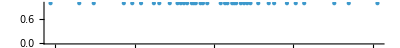

```mathematica
NumberLinePlot[symRange]
```

A transcendental range with negative step:

```mathematica
negStepRange=TranscendentalRange[100,1,-1]
```

{36 ⅇ,13 ⅇ^2,35 ⅇ,34 ⅇ,33 ⅇ,12 ⅇ^2,32 ⅇ,31 ⅇ,30 ⅇ,11 ⅇ^2,4 ⅇ^3,29 ⅇ,28 ⅇ,10 ⅇ^2,27 ⅇ,26 ⅇ,25 ⅇ,9 ⅇ^2,24 ⅇ,23 ⅇ,3 ⅇ^3,22 ⅇ,8 ⅇ^2,21 ⅇ,ⅇ^4,20 ⅇ,7 ⅇ^2,19 ⅇ,18 ⅇ,17 ⅇ,6 ⅇ^2,16 ⅇ,15 ⅇ,2 ⅇ^3,14 ⅇ,5 ⅇ^2,13 ⅇ,12 ⅇ,11 ⅇ,4 ⅇ^2,10 ⅇ,9 ⅇ,3 ⅇ^2,8 ⅇ,ⅇ^3,7 ⅇ,6 ⅇ,2 ⅇ^2,5 ⅇ,4 ⅇ,3 ⅇ,ⅇ^2,2 ⅇ,ⅇ}

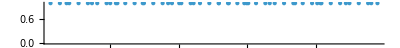

```mathematica
NumberLinePlot[negStepRange]
```

Require a lower bound on the steps:

```mathematica
boundedRange=TranscendentalRange[-2,2,1/4,1/8]
```

{-(3 ⅇ^(1/4))/2,-ⅇ^(5/4)/2,-(5 ⅇ^(1/4))/4,-ⅇ^(7/4)/4,-ⅇ^(1/4),-ⅇ^(3/2)/4,-5/(4 ⅇ^(1/4)),-7/(4 ⅇ^(3/4)),-ⅇ/4,-3/(2 ⅇ),-(√ⅇ)/4,-1/ⅇ^(5/4),-1/(4 √ⅇ),1/(4 ⅇ^2),3/(4 ⅇ^(3/2)),1/(2 √ⅇ),3/(2 ⅇ^(5/4)),2/ⅇ^(5/4),3/(2 ⅇ^(3/4)),ⅇ^(5/4)/4,ⅇ^(3/4)/2,2/(√ⅇ),ⅇ/2,2/ⅇ^(1/4),ⅇ^(5/4)/2,(3 ⅇ^(1/4))/2}

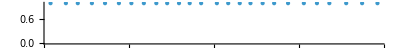

```mathematica
NumberLinePlot[boundedRange]
```

A very large transcendental range generated efficiently:

```mathematica
largeRange=TranscendentalRange[-100,100,1/2]//EchoTiming
```

2.2326

```mathematica
Length[largeRange]
```

80604

### Options

#### Method

A range in terms of logarithms:

```mathematica
logRange=TranscendentalRange[10,Method->Log]
```

{Log[3],2 Log[2],Log[5],Log[6],Log[7],3 Log[2],2 Log[3],Log[10],4 Log[2],2 Log[5],3 Log[3],5 Log[2],2 Log[6],2 Log[7],6 Log[2],4 Log[3],2 Log[10],3 Log[5],7 Log[2],3 Log[6],5 Log[3],8 Log[2],3 Log[7],3 Log[8],9 Log[2],4 Log[5],6 Log[3],3 Log[10],10 Log[2],4 Log[6],7 Log[3],4 Log[7],5 Log[5],6 Log[4],8 Log[3],5 Log[6],4 Log[10],6 Log[5],7 Log[4],5 Log[7],9 Log[3]}

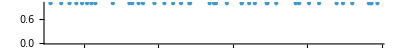

```mathematica
NumberLinePlot[logRange]
```

Ranges in terms of hyperbolic transcendental functions:

```mathematica
TranscendentalRange[-10,10,Method->Sinh]
```

{-8 Sinh[1],-7 Sinh[1],-2 Sinh[2],-6 Sinh[1],-5 Sinh[1],-4 Sinh[1],-Sinh[2],-3 Sinh[1],-2 Sinh[1],-Sinh[1],Sinh[1],2 Sinh[1],3 Sinh[1],Sinh[2],4 Sinh[1],5 Sinh[1],6 Sinh[1],2 Sinh[2],7 Sinh[1],8 Sinh[1]}

```mathematica
TranscendentalRange[3,7,Method->Tanh]
```

{4 Tanh[3],4 Tanh[4],4 Tanh[5],4 Tanh[6],4 Tanh[7],5 Tanh[3],5 Tanh[4],5 Tanh[5],5 Tanh[6],5 Tanh[7],6 Tanh[3],6 Tanh[4],6 Tanh[5],6 Tanh[6],6 Tanh[7],7 Tanh[3],7 Tanh[4],7 Tanh[5],7 Tanh[6],7 Tanh[7]}

Ranges in terms of inverse hyperbolic functions:

```mathematica
TranscendentalRange[-2,2,Method->ArcSinh]
```

{-2 ArcSinh[1],-ArcSinh[2],-ArcSinh[1],ArcSinh[1],ArcSinh[2],2 ArcSinh[1]}

```mathematica
TranscendentalRange[-2,2,1/2,Method->ArcTanh]
```

{-2 ArcTanh[1/2],-3/2 ArcTanh[1/2],-ArcTanh[1/2],-1/2 ArcTanh[1/2],1/2 ArcTanh[1/2],ArcTanh[1/2],3/2 ArcTanh[1/2],2 ArcTanh[1/2]}

Ranges in terms of trigonometric functions:

```mathematica
TranscendentalRange[-2,2,Method->Sin]
```

{-2 Sin[2],-2 Sin[1],-Sin[2],-Sin[1],Sin[1],Sin[2],2 Sin[1],2 Sin[2]}

```mathematica
TranscendentalRange[-2,2,Method->Csc]
```

{-Csc[1],-Csc[2],Csc[2],Csc[1]}

Ranges in terms of inverse trigonometric functions:

```mathematica
TranscendentalRange[-2,2,Method->ArcTan]
```

{-π/2,-ArcTan[2],-π/4,π/4,ArcTan[2],π/2}

```mathematica
TranscendentalRange[-2,2,Method->ArcCsc]
```

{-π/2,-π/3,-π/6,π/6,π/3,π/2}

Ranges in terms of Power (this requires the setting "GeneratorsDomain"->Algebraics to get non-trivial results):

```mathematica
TranscendentalRange[-3,3,Method->Power,"GeneratorsDomain"->Algebraics]
```

{3^(-2 √2),2^(-3 √2),3^(-√7),7^(-√2),2^(-(3 √7)/2),3^(-√6),7^(-(√7)/2),(2 √2)^(-√6),6^(-√2),3^(-√5),7^(-√(3/2)),6^(-(√7)/2),2^(-(3 √5)/2),5^(-√2),6^(-√(3/2)),7^(-(√5)/2),5^(-(√7)/2),6^(-(√5)/2),5^(-√(3/2)),2^(-2 √2),3^(-√3),2^(-√7),2^(-(3 √3)/2),5^(-(√5)/2),2^(-√6),7^(-(√3)/2),3^(-√2),6^(-(√3)/2),2^(-√5),(2 √2)^(-√2),3^(-(√7)/2),5^(-(√3)/2),7^(-1/(√2)),3^(-√(3/2)),6^(-1/(√2)),3^(-(√5)/2),2^(-√3),5^(-1/(√2)),2^(-√2),3^(-(√3)/2),2^(-(√7)/2),2^(-√(3/2)),3^(-1/(√2)),2^(-(√5)/2),2^(-(√3)/2),2^(-1/(√2)),2^(1/(√2)),2^((√3)/2),2^((√5)/2),3^(1/(√2)),2^(√(3/2)),2^((√7)/2),3^((√3)/2),2^(√2)}

A range in terms of a list of different types:

```mathematica
TranscendentalRange[-4,4,Method->{ArcCot,Exp}]
```

{-π,-ⅇ,-(3 π)/4,-4 ArcCot[2],-π/2,-4/ⅇ,-3 ArcCot[2],-4 ArcCot[3],-3/ⅇ,-4 ArcCot[4],-3 ArcCot[3],-2 ArcCot[2],-π/4,-2/ⅇ,-3 ArcCot[4],-2 ArcCot[3],-4/ⅇ^2,-2 ArcCot[4],-ArcCot[2],-3/ⅇ^2,-1/ⅇ,-ArcCot[3],-2/ⅇ^2,-ArcCot[4],-4/ⅇ^3,-3/ⅇ^3,-1/ⅇ^2,-2/ⅇ^3,-4/ⅇ^4,-3/ⅇ^4,-1/ⅇ^3,-2/ⅇ^4,-1/ⅇ^4,1/ⅇ^4,2/ⅇ^4,1/ⅇ^3,3/ⅇ^4,4/ⅇ^4,2/ⅇ^3,1/ⅇ^2,3/ⅇ^3,4/ⅇ^3,ArcCot[4],2/ⅇ^2,ArcCot[3],1/ⅇ,3/ⅇ^2,ArcCot[2],2 ArcCot[4],4/ⅇ^2,2 ArcCot[3],3 ArcCot[4],2/ⅇ,π/4,2 ArcCot[2],3 ArcCot[3],4 ArcCot[4],3/ⅇ,4 ArcCot[3],3 ArcCot[2],4/ⅇ,π/2,4 ArcCot[2],(3 π)/4,ⅇ,π}

A range in terms of all previous types combined:

```mathematica
completeRange=TranscendentalRange[3,Method->All]
```

{Coth[3],3 ArcCsc[3],Coth[2],3 ArcCoth[3],π/3,2 Cos[1],Log[3],Csc[2],ArcTan[2],Sinh[1],Csc[1],ArcSec[3],ArcTan[3],2 Cot[1],2 Sech[1],Coth[1],ArcCosh[2],2 Log[2],3 ArcCot[2],ArcSinh[2],2 Tanh[1],Cosh[1],Tan[1],π/2,3 Cos[1],3 ArcCoth[2],2 Sin[1],2 Csch[1],2 ArcSinh[1],ArcSinh[3],2 Sin[2],Sec[1],3 Cot[1],2 Tanh[2],3 Sech[1],2 Tanh[3],2 Coth[3],2 Coth[2],3 Log[2],(2 π)/3,2 Log[3],2 Csc[2],2 ArcTan[2],3 Tanh[1],2 Sinh[1],(3 π)/4,2 Csc[1],2 ArcSec[3],2 ArcTan[3],3 Sin[1],3 Csch[1],2 Coth[1],2 ArcCosh[2],3 ArcSinh[1],ⅇ,3 Sin[2],2 ArcSinh[2],3 Tanh[2],3 Tanh[3]}

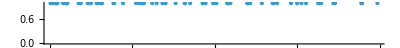

```mathematica
NumberLinePlot[completeRange]
```

#### Multiplicity

Linear combinations of exponentials are still transcendental numbers:

```mathematica
rangeMult2=TranscendentalRange[0,6,1/2,"Multiplicity"->2]
```

{√ⅇ,(√ⅇ)/2+ⅇ/2,(3 √ⅇ)/2,ⅇ,√ⅇ+ⅇ/2,(√ⅇ)/2+ⅇ^(3/2)/2,2 √ⅇ,(√ⅇ)/2+ⅇ,ⅇ/2+ⅇ^(3/2)/2,(3 √ⅇ)/2+ⅇ/2,√ⅇ+ⅇ^(3/2)/2,(3 ⅇ)/2,(5 √ⅇ)/2,√ⅇ+ⅇ,ⅇ^(3/2),(√ⅇ)/2+ⅇ^2/2,2 √ⅇ+ⅇ/2,(3 √ⅇ)/2+ⅇ^(3/2)/2,(√ⅇ)/2+(3 ⅇ)/2,3 √ⅇ,ⅇ+ⅇ^(3/2)/2,ⅇ/2+ⅇ^2/2,(3 √ⅇ)/2+ⅇ,(√ⅇ)/2+ⅇ^(3/2),√ⅇ+ⅇ^2/2,2 ⅇ,(5 √ⅇ)/2+ⅇ/2,2 √ⅇ+ⅇ^(3/2)/2,√ⅇ+(3 ⅇ)/2,(7 √ⅇ)/2,ⅇ/2+ⅇ^(3/2),ⅇ^(3/2)/2+ⅇ^2/2}

```mathematica
rangeMult3=TranscendentalRange[0,6,1/2,"Multiplicity"->3]
```

{(3 √ⅇ)/2,√ⅇ+ⅇ/2,2 √ⅇ,(√ⅇ)/2+ⅇ,(3 √ⅇ)/2+ⅇ/2,√ⅇ+ⅇ^(3/2)/2,(3 ⅇ)/2,(5 √ⅇ)/2,√ⅇ+ⅇ,(√ⅇ)/2+ⅇ/2+ⅇ^(3/2)/2,2 √ⅇ+ⅇ/2,(3 √ⅇ)/2+ⅇ^(3/2)/2,(√ⅇ)/2+(3 ⅇ)/2,3 √ⅇ,ⅇ+ⅇ^(3/2)/2,(3 √ⅇ)/2+ⅇ,√ⅇ+ⅇ/2+ⅇ^(3/2)/2,(√ⅇ)/2+ⅇ^(3/2),√ⅇ+ⅇ^2/2,2 ⅇ,(5 √ⅇ)/2+ⅇ/2,2 √ⅇ+ⅇ^(3/2)/2,√ⅇ+(3 ⅇ)/2,(7 √ⅇ)/2,(√ⅇ)/2+ⅇ+ⅇ^(3/2)/2,ⅇ/2+ⅇ^(3/2),(√ⅇ)/2+ⅇ/2+ⅇ^2/2}

The method Power combines through products:

```mathematica
TranscendentalRange[-1/2,3/2,1/2,Method->Power,"GeneratorsDomain"->Algebraics,"Multiplicity"->2]
```

{2^(-2 √2),2^(-1/(√2)-√2),2^(-1/(2 √2)-√2),2^(-√2),2^(-3/(2 √2)),2^(-1/(√2)-√2) 3^(1/(√2)),2^(-1/(√2)),2^(-1/(2 √2)),(3/4)^(1/(√2)),2^(-3/(2 √2)) 3^(1/(√2))}

Different methods combine only within themselves:

```mathematica
TranscendentalRange[-1/2,3/2,1/2,Method->{Exp,Log},"Multiplicity"->2]
```

{-Log[3/2],1/2 Log[3/2]-Log[2]/2,Log[3/2]-Log[2]/2,-1/2 Log[3/2]+Log[2]/2,1/2 Log[3/2],3/2 Log[3/2]-Log[2]/2,1/(2 √ⅇ),Log[3/2],-1/(2 √ⅇ)+(√ⅇ)/2,1/2 Log[3/2]+Log[2]/2,1/(√ⅇ),3/2 Log[3/2],Log[2],Log[3/2]+Log[2]/2,2 Log[3/2],3/(2 √ⅇ),3/2 Log[3/2]+Log[2]/2,5/2 Log[3/2],-1/(2 √ⅇ)+ⅇ/2,1/(2 √ⅇ)+(√ⅇ)/2,2/(√ⅇ),3 Log[3/2],1/(√ⅇ)+(√ⅇ)/2}

#### GeneratorsDomain

A transcendental range generated by non rationals Algebraics:

```mathematica
algRange=TranscendentalRange[8,"GeneratorsDomain"->Algebraics]
```

{ⅇ,√2 ⅇ,ⅇ^(√2),√3 ⅇ,2 ⅇ,ⅇ^(√3),√2 ⅇ^(√2),√5 ⅇ,√6 ⅇ,√3 ⅇ^(√2),√7 ⅇ,ⅇ^2,2 √2 ⅇ,√2 ⅇ^(√3)}

Compare with the corresponding default range in terms of the default Rationals:

```mathematica
ratRange=TranscendentalRange[8,"GeneratorsDomain"->Rationals]
```

{ⅇ,2 ⅇ,ⅇ^2}

```mathematica
SubsetQ[algRange,ratRange]
```

True

#### FareyRange

Generate steps according to the FareySequence:

```mathematica
farRange=TranscendentalRange[1,10,1/3,"FareyRange"->True]
```

{ⅇ,(4 ⅇ)/3,ⅇ^(4/3),(3 ⅇ)/2,ⅇ^(3/2),(5 ⅇ)/3,(4 ⅇ^(4/3))/3,ⅇ^(5/3),2 ⅇ,(3 ⅇ^(4/3))/2,(4 ⅇ^(3/2))/3,(5 ⅇ^(4/3))/3,(7 ⅇ)/3,(3 ⅇ^(3/2))/2,(5 ⅇ)/2,(4 ⅇ^(5/3))/3,(8 ⅇ)/3,ⅇ^2,(5 ⅇ^(3/2))/3,2 ⅇ^(4/3),(3 ⅇ^(5/3))/2,3 ⅇ,(5 ⅇ^(5/3))/3,(7 ⅇ^(4/3))/3,2 ⅇ^(3/2),(10 ⅇ)/3,(5 ⅇ^(4/3))/2,(7 ⅇ)/2,(4 ⅇ^2)/3,(11 ⅇ)/3}

Compare with the default transcendental range of step 1/2:

```mathematica
range1over2=TranscendentalRange[1,10,1/2,"FareyRange"->False]
```

{ⅇ,(3 ⅇ)/2,ⅇ^(3/2),2 ⅇ,(3 ⅇ^(3/2))/2,(5 ⅇ)/2,ⅇ^2,3 ⅇ,2 ⅇ^(3/2),(7 ⅇ)/2}

Also the default transcendental range of step 1/3:

```mathematica
range1over3=TranscendentalRange[1,10,1/3,"FareyRange"->False]
```

{ⅇ,(4 ⅇ)/3,ⅇ^(4/3),(5 ⅇ)/3,(4 ⅇ^(4/3))/3,ⅇ^(5/3),2 ⅇ,(5 ⅇ^(4/3))/3,(7 ⅇ)/3,(4 ⅇ^(5/3))/3,(8 ⅇ)/3,ⅇ^2,2 ⅇ^(4/3),3 ⅇ,(5 ⅇ^(5/3))/3,(7 ⅇ^(4/3))/3,(10 ⅇ)/3,(4 ⅇ^2)/3,(11 ⅇ)/3}

It turns out that the transcendental Farey range does not correspond to simply combining ordinary ranges with more steps, but to a superset of it:

```mathematica
range1over2over3=SortBy[DeleteDuplicatesBy[Join[range1over2,range1over3],N],N]
```

{ⅇ,(4 ⅇ)/3,ⅇ^(4/3),(3 ⅇ)/2,ⅇ^(3/2),(5 ⅇ)/3,(4 ⅇ^(4/3))/3,ⅇ^(5/3),2 ⅇ,(5 ⅇ^(4/3))/3,(7 ⅇ)/3,(3 ⅇ^(3/2))/2,(5 ⅇ)/2,(4 ⅇ^(5/3))/3,(8 ⅇ)/3,ⅇ^2,2 ⅇ^(4/3),3 ⅇ,(5 ⅇ^(5/3))/3,(7 ⅇ^(4/3))/3,2 ⅇ^(3/2),(10 ⅇ)/3,(7 ⅇ)/2,(4 ⅇ^2)/3,(11 ⅇ)/3}

```mathematica
SubsetQ[farRange,range1over2over3]
```

True

Create a transcendental Farey range including root arguments:

```mathematica
algFareyRange=TranscendentalRange[0,3/2,1/3,"FareyRange"->True,"GeneratorsDomain"->Algebraics]
```

{ⅇ^(1/3)/3,ⅇ^((√2)/3)/3,(√ⅇ)/3,ⅇ^(2/3)/3,1/3 √2 ⅇ^(1/3),ⅇ^(1/(√2))/3,ⅇ^(1/3)/2,1/3 √2 ⅇ^((√2)/3),(√(2 ⅇ))/3,ⅇ^((√2)/3)/2,(√ⅇ)/2,1/3 ⅇ^((2 √2)/3),ⅇ/3,1/3 √2 ⅇ^(2/3),(2 ⅇ^(1/3))/3,1/3 √2 ⅇ^(1/(√2)),ⅇ^(2/3)/2,ⅇ^(1/3)/(√2),ⅇ^(1/(√2))/2,(2 ⅇ^((√2)/3))/3,(2 √ⅇ)/3,ⅇ^((√2)/3)/(√2),√(ⅇ/2),1/3 √2 ⅇ^((2 √2)/3),ⅇ^(4/3)/3,(√2 ⅇ)/3,1/2 ⅇ^((2 √2)/3),(2 ⅇ^(2/3))/3,2/3 √2 ⅇ^(1/3),(2 ⅇ^(1/(√2)))/3,ⅇ/2,ⅇ^(√2)/3,ⅇ^(2/3)/(√2),ⅇ^(1/3),ⅇ^(1/(√2))/(√2),ⅇ^(3/2)/3}

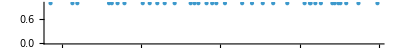

```mathematica
NumberLinePlot[algFareyRange]
```

#### FormulaComplexity

Reduce the output range by setting a threshold on the complexity:

```mathematica
TranscendentalRange[0,8,1/2,"GeneratorsDomain"->Algebraics,"FormulaComplexity"->5]
```

{ⅇ/2,√ⅇ,ⅇ/(√2),ⅇ^(1/(√2)),ⅇ,2 √ⅇ,ⅇ^2/2,√2 ⅇ,(3 ⅇ)/2,ⅇ^(√2),ⅇ^(3/2),3 √ⅇ,2 ⅇ,4 √ⅇ,(5 ⅇ)/2,ⅇ^2}

Compare with the default range with no complexity threshold:

```mathematica
TranscendentalRange[0,8,1/2,"GeneratorsDomain"->Algebraics,"FormulaComplexity"->Infinity]//Length
```

382

Compare with the same range restricted by the fourth argument (lower bound on steps):

```mathematica
TranscendentalRange[0,8,1/2,2/3,"GeneratorsDomain"->Algebraics,"FormulaComplexity"->Infinity]
```

{(√ⅇ)/2,ⅇ^((√5)/2)/2,ⅇ^(3/2)/2,ⅇ^(√2)/(√2),(√(19 ⅇ))/2,(3 √(3 ⅇ))/2,1/2 √7 ⅇ^((√7)/2),1/2 √11 ⅇ^(√(3/2)),1/2 √5 ⅇ^(√3),ⅇ^((√21)/2)/(√2),√(5/2) ⅇ^(√(5/2))}

#### WorkingPrecision

In certain cases the generated symbolic expressions may be found to collide in terms of their N numerical values:

```mathematica
machPrecRange=TranscendentalRange[20,25,Method->Tanh]
```

{21 Tanh[20],22 Tanh[20],23 Tanh[20],24 Tanh[20],25 Tanh[20]}

```mathematica
N[machPrecRange,$MachinePrecision]
```

{21.,22.,23.,24.,25.}

To distinguish them, WorkingPrecision may be optionally set to a higher value:

```mathematica
highPrecRange=TranscendentalRange[20,25,Method->Tanh,WorkingPrecision->30]
```

{21 Tanh[20],21 Tanh[21],21 Tanh[22],21 Tanh[23],21 Tanh[24],21 Tanh[25],22 Tanh[20],22 Tanh[21],22 Tanh[22],22 Tanh[23],22 Tanh[24],22 Tanh[25],23 Tanh[20],23 Tanh[21],23 Tanh[22],23 Tanh[23],23 Tanh[24],23 Tanh[25],24 Tanh[20],24 Tanh[21],24 Tanh[22],24 Tanh[23],24 Tanh[24],24 Tanh[25],25 Tanh[20],25 Tanh[21],25 Tanh[22],25 Tanh[23],25 Tanh[24],25 Tanh[25]}

```mathematica
N[highPrecRange,30]
```

{20.9999999999999998215691212778,20.99999999999999997585200649,20.9999999999999999967319244587,20.999999999999999999557714071,20.9999999999999999999401431085,20.9999999999999999999918992506,21.9999999999999998130724127672,21.9999999999999999747021020371,21.9999999999999999965763018139,21.9999999999999999995366528363,21.9999999999999999999372927804,21.9999999999999999999915135007,22.9999999999999998045757042566,22.9999999999999999735521975842,22.9999999999999999964206791691,22.9999999999999999995155916016,22.9999999999999999999344424522,22.9999999999999999999911277507,23.999999999999999796078995746,23.9999999999999999724022931314,23.9999999999999999962650565243,23.9999999999999999994945303668,23.999999999999999999931592124,23.9999999999999999999907420007,24.9999999999999997875822872354,24.9999999999999999712523886785,24.9999999999999999961094338794,24.9999999999999999994734691321,24.9999999999999999999287417959,24.9999999999999999999903562508}

### Applications

Search and find closed forms in terms of exponentials:

```mathematica
ResourceFunction["FindClosedForm"][
1.922115514,Identity,
"SearchRange"->Function[Range[#]~Join~TranscendentalRange[#]]]
```

ⅇ/(√2)

```mathematica
N[%,10]
```

1.922115514

Find closed forms in terms of all elementary transcendental functions:

```mathematica
ResourceFunction["FindClosedForm"][
1.162002218,Identity,
"SearchRange"->Function[Range[#]~Join~TranscendentalRange[1,#,1/#,Method->All]],
"MonitorSearch"->True]
```

-1/8+2 ArcCot[4/3]

```mathematica
N[%,10]
```

1.162002218

Find closed forms in terms of common mathematical functions composed to exponentials:

```mathematica
ResourceFunction["FindClosedForm"][
9.095468039,
"SearchRange"->Function[Range[#]~Join~TranscendentalRange[#]],
"MonitorSearch"->True,
"FormulaComplexity"->50]
```

-1500+Gamma[ⅇ^2]

```mathematica
N[%,10]
```

9.095468039

Search and find closed forms in terms of common functions composed to any of the available transcendental functions:

```mathematica
ResourceFunction["FindClosedForm"][
-0.01020330726,
"SearchRange"->Function[Range[-#,#]~Join~TranscendentalRange[-#,#,Method->All]],
"MonitorSearch"->True]
```

1/4 Zeta[-ArcTan[4]]

### Properties and Relations

TranscendentalRange[x,y,z] can be simply generated through the Outer product of the function #1 Exp[#2]&, with both arguments running over Range[x,y,z], suitably restricted to the elements within the bounds x, y, not belonging to the Algebraics and sorted, as follows:

```mathematica
outerTranscRange[x_,y_,z_]/;z>0:=
SortBy[DeleteDuplicatesBy[
Select[
Outer[# Exp[#2]&,Range[x,y,z],Range[x,y,z]]//Flatten,
x<=#<=y&&!Element[#,Algebraics]&],N],N]
```

```mathematica
outerRange=outerTranscRange[-2,2,1/2]
```

{-√ⅇ,-ⅇ/2,-2/(√ⅇ),-3/(2 √ⅇ),-(√ⅇ)/2,-2/ⅇ,-1/(√ⅇ),-3/(2 ⅇ),-2/ⅇ^(3/2),-1/ⅇ,-3/(2 ⅇ^(3/2)),-1/(2 √ⅇ),-2/ⅇ^2,-1/ⅇ^(3/2),-3/(2 ⅇ^2),-1/(2 ⅇ),-1/ⅇ^2,-1/(2 ⅇ^(3/2)),-1/(2 ⅇ^2),1/(2 ⅇ^2),1/(2 ⅇ^(3/2)),1/ⅇ^2,1/(2 ⅇ),3/(2 ⅇ^2),1/ⅇ^(3/2),2/ⅇ^2,1/(2 √ⅇ),3/(2 ⅇ^(3/2)),1/ⅇ,2/ⅇ^(3/2),3/(2 ⅇ),1/(√ⅇ),2/ⅇ,(√ⅇ)/2,3/(2 √ⅇ),2/(√ⅇ),ⅇ/2,√ⅇ}

```mathematica
transcRange=TranscendentalRange[-2,2,1/2]
```

{-√ⅇ,-ⅇ/2,-2/(√ⅇ),-3/(2 √ⅇ),-(√ⅇ)/2,-2/ⅇ,-1/(√ⅇ),-3/(2 ⅇ),-2/ⅇ^(3/2),-1/ⅇ,-3/(2 ⅇ^(3/2)),-1/(2 √ⅇ),-2/ⅇ^2,-1/ⅇ^(3/2),-3/(2 ⅇ^2),-1/(2 ⅇ),-1/ⅇ^2,-1/(2 ⅇ^(3/2)),-1/(2 ⅇ^2),1/(2 ⅇ^2),1/(2 ⅇ^(3/2)),1/ⅇ^2,1/(2 ⅇ),3/(2 ⅇ^2),1/ⅇ^(3/2),2/ⅇ^2,1/(2 √ⅇ),3/(2 ⅇ^(3/2)),1/ⅇ,2/ⅇ^(3/2),3/(2 ⅇ),1/(√ⅇ),2/ⅇ,(√ⅇ)/2,3/(2 √ⅇ),2/(√ⅇ),ⅇ/2,√ⅇ}

```mathematica
outerRange==transcRange
```

True

The actual implementation of TranscendentalRange[x,y,z] is much more efficient than Outer over large exponentially increasing ranges:

```mathematica
outerRange=outerTranscRange[1,1000,1];//AbsoluteTiming
```

{11.1612,Null}

```mathematica
transcRange=TranscendentalRange[1000];//AbsoluteTiming
```

{0.047206,Null}

```mathematica
outerRange==transcRange
```

True

### Possible Issues

By definition, the arguments must be all algebraic numbers:

```mathematica
TranscendentalRange[0,E,1/3]
```

Failure[…]

Bypassed this limitation by increasing the arguments:

```mathematica
TranscendentalRange[0,Ceiling[E],1/3]
```

{ⅇ^(1/3)/3,ⅇ^(2/3)/3,ⅇ/3,(2 ⅇ^(1/3))/3,ⅇ^(4/3)/3,(2 ⅇ^(2/3))/3,ⅇ^(1/3),ⅇ^(5/3)/3,(2 ⅇ)/3,(4 ⅇ^(1/3))/3,ⅇ^(2/3),(5 ⅇ^(1/3))/3,ⅇ^2/3,(2 ⅇ^(4/3))/3,(4 ⅇ^(2/3))/3,ⅇ,2 ⅇ^(1/3)}

### Neat Examples

Generate a mixed large transcendental range with all the methods available:

```mathematica
mixedRange=TranscendentalRange[-2,2,1/3,Method->All,"FareyRange"->True,"GeneratorsDomain"->Algebraics];
```

```mathematica
Length[mixedRange]
```

8878

```mathematica
RandomSample[mixedRange,10]
```

{√3 Tanh[√3],(2 Coth[4/3])/(√3),(3 Cot[1])/2,-(2 ArcSinh[1])/(√3),-1/2 ⅇ^(-(4 √2)/3),3/2 ⅇ^(-(√3)/2),√2 Csch[(4 √2)/3],-1/2 Csc[√2],-2 ArcTan[1/3],-1/3 Sinh[(2 √2)/3]}

Pick a random element of it and verify experimentally the property of being transcendental, that is that its RootApproximant expressions do not converge at any given precision:

```mathematica
randTransc=RandomChoice[mixedRange]
```

-ArcSec[-(4 √2)/3]/(√3)

```mathematica
(*Warning: the following computation can take a few minutes!*)
```

```mathematica
Table[
{prec,Magnify[InputForm@RootApproximant@N[randTransc,prec],0.7]},{prec,PowerRange[16,512,2]}]//Grid@Prepend[#,{"Precision","RootApproximant"}]&
```

Precision | RootApproximant
16 | Root[2 - 2*#1 - 2*#1^6 - 2*#1^7 - #1^11 + #1^12 - #1^13 - 2*#1^14 + #1^16 + #1^17 & , 1, 0]
32 | Root[2 + 3*#1^2 + 3*#1^3 - 4*#1^4 - #1^5 + 6*#1^6 + 2*#1^7 - 4*#1^8 - 2*#1^9 - 6*#1^10 - 3*#1^11 - 4*#1^12 - 6*#1^13 - 2*#1^14 - 2*#1^16 + 2*#1^17 + 7*#1^18 - 3*#1^20 + 2*#1^21 + 2*#1^22 & , 1, 0]
64 | Root[9 + 9*#1^2 + 11*#1^3 - 18*#1^4 + 9*#1^5 - 2*#1^6 + 2*#1^7 + 3*#1^8 - 2*#1^9 - 6*#1^10 - 9*#1^11 + 4*#1^12 + 6*#1^13 - 19*#1^14 - 8*#1^15 + 15*#1^16 + 6*#1^17 + #1^18 - 2*#1^19 + 18*#1^20 - 2*#1^21 + #1^22 + 6*#1^23 - 11*#1^24 + 4*#1^25 - 16*#1^26 - 7*#1^27 + 4*#1^28 - #1^29 - 9*#1^30 + 17*#1^31 - 4*#1^32 + 7*#1^33 - #1^34 - 3*#1^35 - 2*#1^36 - #1^38 - 3*#1^39 - #1^40 - 6*#1^41 + #1^42 - #1^43 - 2*#1^44 - 2*#1^45 - 2*#1^46 + #1^47 + #1^48 & , 1, 0]
128 | Root[-623 + 62*#1 - 511*#1^2 - 84*#1^3 + 815*#1^4 + 1010*#1^5 + 1016*#1^6 + 2119*#1^7 + 629*#1^8 - 13*#1^9 - 534*#1^10 + 532*#1^11 + 485*#1^12 - 135*#1^13 + 582*#1^14 - 597*#1^15 + 112*#1^16 - 133*#1^17 - 441*#1^18 - 577*#1^19 - 81*#1^20 + 1666*#1^21 + 602*#1^22 - 1224*#1^23 + 1217*#1^24 - 193*#1^25 - 730*#1^26 - 334*#1^27 - 942*#1^28 - 802*#1^29 + 784*#1^30 + 296*#1^31 + 528*#1^32 + 1121*#1^33 + 260*#1^34 + 186*#1^35 + 25*#1^36 - 112*#1^37 - 51*#1^38 + 3*#1^39 & , 1, 0]
256 | Root[1198316380 + 2180314257*#1 - 525363831*#1^2 + 1779499809*#1^3 - 1664786617*#1^4 + 1491163765*#1^5 + 1519767943*#1^6 + 508449621*#1^7 - 3302495916*#1^8 + 1819657398*#1^9 + 1794126776*#1^10 + 4499583*#1^11 + 611733447*#1^12 + 7394465177*#1^13 - 2056154399*#1^14 + 146795251*#1^15 + 5939698986*#1^16 + 2437930505*#1^17 - 1576340912*#1^18 + 1150344869*#1^19 - 1051538052*#1^20 - 6845865320*#1^21 - 839827779*#1^22 - 668418517*#1^23 - 1737817594*#1^24 + 38617*#1^25 & , 2, 0]
512 | Root[261814564129 - 319658680198*#1 + 135019311960*#1^2 - 840798923263*#1^3 + 289984610740*#1^4 + 1459330927775*#1^5 + 27100772004*#1^6 - 316754383253*#1^7 + 2807525969127*#1^8 + 1751121474905*#1^9 - 570433618930*#1^10 + 969880285822*#1^11 - 770767838144*#1^12 + 386171020078*#1^13 - 1432145214060*#1^14 - 3422755539760*#1^15 + 1807190110367*#1^16 + 1858847789099*#1^17 + 987108418920*#1^18 + 1497242318920*#1^19 - 1315286140853*#1^20 - 1845842381564*#1^21 - 1196290431098*#1^22 + 442827516064*#1^23 + 2038477618035*#1^24 - 467208524631*#1^25 + 3955596566536*#1^26 + 2844623837595*#1^27 - 3272874966548*#1^28 - 373512273033*#1^29 - 218469492184*#1^30 + 53188655819*#1^31 - 556891640368*#1^32 - 632613824934*#1^33 + 1112576099510*#1^34 + 906232177784*#1^35 - 674267712808*#1^36 - 1389074810611*#1^37 - 925957481697*#1^38 - 370909873892*#1^39 + 5215*#1^40 & , 1, 0]

It is interesting to do the same computation on algebraic numbers. Install this paclet to generate more general algebraic numbers:

```mathematica
PacletInstall["DanieleGregori/GeneralizedRange"]
```

PacletObject[…]

```mathematica
Get["DanieleGregori`GeneralizedRange`"]
```

Generate a large algebraic range and pick a random algebraic number in it:

```mathematica
largeAlgebraicRange={{-Graphics-, AlgebraicRange}}[-3,3,1/2,"RootOrder"->3,Method->All];
```

```mathematica
Length[largeAlgebraicRange]
```

17943

```mathematica
randAlg=RandomChoice@largeAlgebraicRange
```

-5^(1/3)/2^(2/3)-23^(1/3)/2

We find for this a quite rapid convergence beyond 64 approximation digits:

```mathematica
Table[
{prec,Magnify[InputForm@RootApproximant@N[randAlg,prec],0.7]},{prec,PowerRange[16,512,2]}]~Prepend~{"Precision","RootApproximant"}//Grid
```

Precision | RootApproximant
16 | Root[2 - #1 - 4*#1^2 + 4*#1^3 - 2*#1^4 + 4*#1^5 + 2*#1^7 - 2*#1^9 - 6*#1^11 + #1^13 & , 1, 0]
32 | Root[1 + 6*#1 - 3*#1^2 - 2*#1^3 - #1^4 - 5*#1^5 + 3*#1^6 + 2*#1^7 - 2*#1^8 - #1^9 - #1^10 - 6*#1^11 - #1^12 - #1^13 + #1^14 - #1^15 + 2*#1^16 + 7*#1^17 - 2*#1^18 + 2*#1^19 + 4*#1^20 + #1^21 & , 1, 0]
64 | Root[35937 - 23544*#1^3 + 6336*#1^6 + 512*#1^9 & , 1, 0]
128 | Root[35937 - 23544*#1^3 + 6336*#1^6 + 512*#1^9 & , 1, 0]
256 | Root[35937 - 23544*#1^3 + 6336*#1^6 + 512*#1^9 & , 1, 0]
512 | Root[35937 - 23544*#1^3 + 6336*#1^6 + 512*#1^9 & , 1, 0]

Find the most complex algebraic in terms of LeafCount:

```mathematica
complexAlg=TakeLargestBy[largeAlgebraicRange,LeafCount,1]//First
```

-√((3 3^(1/3))/2^(2/3)+√(3/2) 7^(1/6))

The convergence of RootApproximant is slower but necessarily happens after about 512 approximation digits:

```mathematica
Table[
{prec,Magnify[InputForm@RootApproximant@N[complexAlg,prec],0.7]},{prec,PowerRange[16,1024,2]}]~Prepend~{"Precision","RootApproximant"}//Grid
```

Precision | RootApproximant
16 | Root[-2 - #1^2 + 4*#1^3 - 2*#1^4 - #1^5 + 3*#1^6 + 4*#1^7 + 2*#1^8 - 2*#1^9 + #1^10 + #1^11 & , 1, 0]
32 | Root[-3 - 3*#1 - 3*#1^2 - 2*#1^3 + 6*#1^4 - #1^5 + #1^6 - #1^7 + 3*#1^8 - 2*#1^9 + 5*#1^10 - 5*#1^13 - 2*#1^14 - #1^15 + 7*#1^16 - #1^17 + 2*#1^18 + 2*#1^19 & , 1, 0]
64 | Root[-6 - 2*#1 - 6*#1^2 - 4*#1^3 + 7*#1^4 + 9*#1^5 + 10*#1^6 - 3*#1^7 - 11*#1^8 + 3*#1^9 - 7*#1^10 - 2*#1^11 + #1^12 - 4*#1^13 + 3*#1^14 + 13*#1^15 + 10*#1^16 + 14*#1^17 + 12*#1^18 + 13*#1^19 + 18*#1^20 + 13*#1^21 + 12*#1^22 + 12*#1^23 + 16*#1^24 + 10*#1^25 + 5*#1^26 + 6*#1^27 + 5*#1^28 + 6*#1^29 + 3*#1^30 + 2*#1^31 + 5*#1^32 + 6*#1^33 + 4*#1^34 + #1^35 & , 1, 0]
128 | Root[15 - 43*#1 + 117*#1^2 + 206*#1^3 - 82*#1^4 + 133*#1^5 - 152*#1^6 + 137*#1^7 - 18*#1^8 - 6*#1^9 - 40*#1^10 - 107*#1^11 + 142*#1^12 + 102*#1^13 - 145*#1^14 - 124*#1^15 + 33*#1^16 - 16*#1^17 - 9*#1^18 - 38*#1^19 - 60*#1^20 - 12*#1^21 + 153*#1^22 + 24*#1^23 + 85*#1^24 + 175*#1^25 + 221*#1^26 - 92*#1^27 - 5*#1^28 + 85*#1^29 + 32*#1^30 + 17*#1^31 - 6*#1^32 - 30*#1^33 + 39*#1^34 + 96*#1^35 + 21*#1^36 - 21*#1^37 + 18*#1^38 - 82*#1^39 + 69*#1^40 - 57*#1^42 - 61*#1^43 + 24*#1^44 + 22*#1^45 + 2*#1^46 - 15*#1^47 - 2*#1^48 - 6*#1^49 + 23*#1^50 + 15*#1^51 + #1^52 & , 2, 0]
256 | Root[984713 + 295442*#1 + 2799770*#1^2 - 196593*#1^3 - 166751*#1^4 - 1007953*#1^5 + 819466*#1^6 + 27332*#1^7 + 114913*#1^8 - 1709838*#1^9 - 1326392*#1^10 - 241929*#1^11 - 2318213*#1^12 + 1686458*#1^13 + 391737*#1^14 + 817944*#1^15 + 452253*#1^16 - 756709*#1^17 + 929653*#1^18 - 1502848*#1^19 - 616246*#1^20 + 257024*#1^21 - 1728340*#1^22 + 1665343*#1^23 + 646867*#1^24 - 573154*#1^25 - 184998*#1^26 + 610346*#1^27 + 613828*#1^28 + 1312139*#1^29 - 58298*#1^30 - 50867*#1^31 + 6573*#1^32 + 435034*#1^33 - 563611*#1^34 - 82465*#1^35 + 225623*#1^36 + 551831*#1^37 - 147875*#1^38 - 186022*#1^39 + 14*#1^40 & , 1, 0]
512 | Root[236372930487 - 206991309384*#1^6 - 6446961072*#1^12 - 974177280*#1^18 + 24903936*#1^24 - 497664*#1^30 + 4096*#1^36 & , 1, 0]
1024 | Root[236372930487 - 206991309384*#1^6 - 6446961072*#1^12 - 974177280*#1^18 + 24903936*#1^24 - 497664*#1^30 + 4096*#1^36 & , 1, 0]

Note this agrees with the minimal polynomial:

```mathematica
MinimalPolynomial[√((3 3^(1/3))/2^(2/3)+√(3/2) 7^(1/6))]
```

236372930487-206991309384 #1^6-6446961072 #1^12-974177280 #1^18+24903936 #1^24-497664 #1^30+4096 #1^36&

Notice the function Element can confirm the algebraic character but not always the transcendental one:

```mathematica
Element[{randAlg,complexAlg},Algebraics]
```

True

```mathematica
Element[randTransc,Algebraics]
```

ArcSec[-(4 √2)/3]∈Algebraics

It should be emphasized though that while these are easy computational investigations within the Wolfram Language, a proper rigorous mathematical proof is necessary to establish the transcendence character of a number (that is equivalent to evaluating it at infinite precision)[1].

It is interesting to notice that according to G. Cantor's theory of infinity, transcendental numbers have higher cardinality - they are in a sense "many more infinite" - than algebraic numbers[2]. This intuitively agrees well also with S. Wolfram's fundamental result showing that computational systems more often exist as a result of the application of rules (or "programs" like Exp) rather than due to the satisfaction of constraints (or "equations" like Root internally) - cf. NKS Ch. 7, p. 342-350[3].

## Source & Additional Information

### Contributed By

Daniele Gregori

### Keywords

transcendental

numbers

range

closed forms

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

Range

Algebraics

E

Pi

### Related Resource Objects

IsTranscendentalNumber

AlgebraicRange

ComplexRange

FareyRange

FindClosedForm

DanieleGregori/GeneralizedRange

### Source/Reference Citation

[1] Alan Baker, Transcendental Number Theory (Cambridge University Press, 1975)
[2] Georg Cantor, Ueber eine Eigenschaft des Inbegriffes aller reellen algebraischen Zahlen (1874)
[3] Stephen Wolfram, A New Kind of Science (Wolfram Media, 2002)

### Links

Transcendental number | Wikipedia

Cantor - On a Property of the Set of All Real Algebraic Numbers

Mathematical Games: mathematical constants | Wolfram Community

### Tests

Compare with test method, which is inefficient but simpler to implement (in terms of Outer instead of monotonicOuter).

#### Tests definition

Generic randomized tests and benchmarks:

```mathematica
ClearAll[testTR]
Options[testTR]={"Timing"->False,"Detail"->False,"GeneratorsDomain"->Rationals,"Multiplicity"->1};

testTR[{f_,ord_},x_,y_,z_,opts:OptionsPattern[testTR]]:=
	Block[{default,testing,timedef,timetest,algGen},
		
algGen=OptionValue["GeneratorsDomain"];
       
{timedef,default}=TranscendentalRange[x,y,z,Method->f,"GeneratorsDomain"->algGen,"Multiplicity"->ord]//AbsoluteTiming;

{timetest,testing}=TranscendentalRange[x,y,z,Method->f,"Test"->True,"GeneratorsDomain"->algGen,"Multiplicity"->ord]//AbsoluteTiming;

If[OptionValue["Timing"],

Module[{gain=timetest/timedef//N,color},
MapThread[Echo,{{timedef,timetest,PercentForm[gain]},{"default","baseline","gain level"}}];
color=Which[
	gain>=10,StandardBlue,
	2<=gain<10,StandardGreen,
	1<gain<2,StandardOrange,
	True,StandardRed];
Echo[color,"gain quality"];
Echo[VerificationTest[gain>1]["Outcome"],"gain test"]]];

If[OptionValue["Detail"],
	VerificationTest[default,testing,SameTest->(N@#1 ==N@#2  &)],
	VerificationTest[N@default==N@testing]]]

testTR[All,{f_,ord_},{m_:0(*lower-bound-like*),c_:20(*upper-bound-like*),s_:2(*step-like*)},opts:OptionsPattern[testTR]]:=
	Block[{det},
		det=Table[
				rg->testTR[{f,ord},rg[[1]],rg[[2]],rg[[3]],"Timing"->False,opts],
			{rg,{{-Abs@m,Abs@c,Abs@s},{Abs@c,-Abs@m,-Abs@s},{-Abs@c,Abs@m,Abs@s},{-Abs@m,Abs@c,-Abs@s},{-Abs@c-Abs@m,Abs@c+Abs@m,Abs@s},{-Abs@c+Abs@m,Abs@c-Abs@m,Abs@s},{Abs@c-Abs@m,-Abs@c+Abs@m,-Abs@s},{Abs@c+Abs@m,-Abs@c-Abs@m,-Abs@s}}}];
		If[OptionValue["Detail"],Echo[det]];
		VerificationTest[And@@Map[#["Outcome"]=="Success"&,Association[det]]]]
```

#### Exp

Tests of correctness:

```mathematica
With[{method=Exp,multi=1},{detailQ=False,tries=5},{diff=10,s=7},With[{args={RandomInteger[{0,5}],RandomInteger[{5+diff,10+diff}],RandomInteger[{1,s}]/RandomInteger[{1,s}]}//Echo},testTR[All,{method,multi},args,"Detail"->detailQ]]~Table~tries]
```

{3,18,7/4}

{2,17,7}

{0,15,1/6}

{1,18,5/4}

{2,18,7/4}

{TestObject[…],TestObject[…],TestObject[…],TestObject[…],TestObject[…]}

Tests of efficiency:

```mathematica
With[{method=Exp,timeQ=True},
With[{args={1,100,1}},
testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.005885

baseline  0.125896

gain level  2139%

gain quality  RGBColor[0.4, 0.6, 1]

gain test  Success

TestObject[…]

```mathematica
With[{method=Exp,timeQ=True},
With[{args={100,-100,-1}},
testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.503904

baseline  0.962138

gain level  190.9%

gain quality  RGBColor[0.98, 0.56, 0.17]

gain test  Success

TestObject[…]

#### Log

Tests of correctness:

```mathematica
With[{method=Log,multi=1},{detailQ=False,tries=5},{diff=10,s=7},With[{args={RandomInteger[{0,5}],RandomInteger[{5+diff,10+diff}],RandomInteger[{1,s}]/RandomInteger[{1,s}]}//Echo},testTR[All,{method,multi},args,"Detail"->detailQ]]~Table~tries]
```

{3,16,1}

{5,15,1/2}

{5,15,6}

{1,19,6/5}

{4,15,6}

{TestObject[…],TestObject[…],TestObject[…],TestObject[…],TestObject[…]}

Tests of efficiency:

```mathematica
With[{method=Log,timeQ=True},
With[{args={1,100,1}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.067418

baseline  0.155841

gain level  231.2%

gain quality  RGBColor[0.14, 0.8, 0.14]

gain test  Success

TestObject[…]

```mathematica
With[{method=Log,timeQ=True},
With[{args={100,-100,-1}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.149684

baseline  0.293504

gain level  196.1%

gain quality  RGBColor[0.98, 0.56, 0.17]

gain test  Success

TestObject[…]

#### Sinh

Tests of correctness:

```mathematica
With[{method=Sinh,multi=1},{detailQ=False,tries=5},{diff=10,s=7},With[{args={RandomInteger[{0,5}],RandomInteger[{5+diff,10+diff}],RandomInteger[{1,s}]/RandomInteger[{1,s}]}//Echo},testTR[All,{method,multi},args,"Detail"->detailQ]]~Table~tries]
```

{5,16,2}

{0,15,3/5}

{5,17,3/2}

{0,16,5/2}

{2,20,2}

{TestObject[…],TestObject[…],TestObject[…],TestObject[…],TestObject[…]}

Tests of efficiency:

```mathematica
With[{method=Sinh,multi=1},{timeQ=True},With[{args={1,100,1}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.008098

baseline  0.139005

gain level  1717%

gain quality  RGBColor[0.4, 0.6, 1]

gain test  Success

TestObject[…]

```mathematica
With[{method=Sinh,multi=1},{timeQ=True},With[{args={100,-100,-1}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.02179

baseline  0.531532

gain level  2439%

gain quality  RGBColor[0.4, 0.6, 1]

gain test  Success

TestObject[…]

#### Cosh

Tests of correctness:

```mathematica
With[{method=Cosh,multi=1},{detailQ=False,tries=5},{diff=10,s=7},With[{args={RandomInteger[{0,5}],RandomInteger[{5+diff,10+diff}],RandomInteger[{1,s}]/RandomInteger[{1,s}]}//Echo},testTR[All,{method,multi},args,"Detail"->detailQ]]~Table~tries]
```

{5,15,2/3}

{1,19,7/2}

{4,16,7/3}

{5,17,3/7}

{5,18,4/3}

{TestObject[…],TestObject[…],TestObject[…],TestObject[…],TestObject[…]}

Tests of efficiency:

```mathematica
With[{method=Cosh,multi=1},{timeQ=True},With[{args={1,100,1}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.008081

baseline  0.1349

gain level  1669%

gain quality  RGBColor[0.4, 0.6, 1]

gain test  Success

TestObject[…]

```mathematica
With[{method=Cosh,multi=1},{timeQ=True},With[{args={100,-100,-1}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.019352

baseline  0.443641

gain level  2292%

gain quality  RGBColor[0.4, 0.6, 1]

gain test  Success

TestObject[…]

#### Tanh

Tests of correctness:

```mathematica
With[{method=Tanh,multi=1},{detailQ=False,tries=5},{diff=5,s=7},With[{args={RandomInteger[{0,5}],RandomInteger[{5+diff,10+diff}],RandomInteger[{1,s}]/RandomInteger[{1,s}]}//Echo},testTR[All,{method,multi},args,"Detail"->detailQ]]~Table~tries]
```

{1,14,2/7}

{0,12,3}

{0,10,4/7}

{0,10,3/2}

{1,13,7/3}

{TestObject[…],TestObject[…],TestObject[…],TestObject[…],TestObject[…]}

Tests of efficiency:

```mathematica
With[{method=Tanh,multi=1},{timeQ=True},With[{args={1,10,1}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.003974

baseline  0.048917

gain level  1231%

gain quality  RGBColor[0.4, 0.6, 1]

gain test  Success

TestObject[…]

```mathematica
With[{method=Tanh,multi=1},{timeQ=True},With[{args={10,-10,-1}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.010459

baseline  0.194952

gain level  1864%

gain quality  RGBColor[0.4, 0.6, 1]

gain test  Success

TestObject[…]

#### Coth

Tests of correctness:

```mathematica
With[{method=Coth,multi=1},{detailQ=False,tries=5},{diff=5,s=7},With[{args={RandomInteger[{0,5}],RandomInteger[{5+diff,10+diff}],RandomInteger[{1,s}]/RandomInteger[{1,s}]}//Echo},testTR[All,{method,multi},args,"Detail"->detailQ]]~Table~tries]
```

{1,13,2/3}

{3,12,7/6}

{2,15,7/6}

{4,10,1}

{0,13,5}

{TestObject[…],TestObject[…],TestObject[…],TestObject[…],TestObject[…]}

Tests of efficiency:

```mathematica
With[{method=Coth,multi=1},{timeQ=True},With[{args={1,30,1}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.025914

baseline  0.787138

gain level  3038%

gain quality  RGBColor[0.4, 0.6, 1]

gain test  Success

TestObject[…]

```mathematica
With[{method=Coth,multi=1},{timeQ=True},With[{args={30,-30,-1}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.084683

baseline  3.11398

gain level  3677%

gain quality  RGBColor[0.4, 0.6, 1]

gain test  Success

TestObject[…]

#### Sech

Tests of correctness:

```mathematica
With[{method=Sech,multi=1},{detailQ=False,tries=5},{diff=10,s=7},With[{args={RandomInteger[{0,5}],RandomInteger[{5+diff,10+diff}],RandomInteger[{1,s}]/RandomInteger[{1,s}]}//Echo},testTR[All,{method,multi},args,"Detail"->detailQ]]~Table~tries]
```

{1,19,4/3}

{2,19,1}

{1,15,4/3}

{0,19,7/4}

{0,18,1/3}

{TestObject[…],TestObject[…],TestObject[…],TestObject[…],TestObject[…]}

Tests of efficiency:

```mathematica
With[{method=Sech,multi=1},{timeQ=True},With[{args={1,100,1}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.024582

baseline  0.163081

gain level  663.4%

gain quality  RGBColor[0.14, 0.8, 0.14]

gain test  Success

TestObject[…]

```mathematica
With[{method=Sech,multi=1},{timeQ=True},With[{args={100,-100,-1}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.971084

baseline  6.62444

gain level  682.2%

gain quality  RGBColor[0.14, 0.8, 0.14]

gain test  Success

TestObject[…]

#### Csch

Tests of correctness:

```mathematica
With[{method=Csch,multi=1},{detailQ=False,tries=5},{diff=5,s=7},With[{args={RandomInteger[{0,5}],RandomInteger[{5+diff,10+diff}],RandomInteger[{1,s}]/RandomInteger[{1,s}]}//Echo},testTR[All,{method,multi},args,"Detail"->detailQ]]~Table~tries]
```

{5,14,1/4}

{2,11,1/3}

{1,12,1/6}

{1,11,1/6}

{0,14,2/5}

{TestObject[…],TestObject[…],TestObject[…],TestObject[…],TestObject[…]}

Tests of efficiency:

```mathematica
With[{method=Csch,multi=1},{timeQ=True},With[{args={1,100,1}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.018381

baseline  0.195291

gain level  1062%

gain quality  RGBColor[0.4, 0.6, 1]

gain test  Success

TestObject[…]

```mathematica
With[{method=Csch,multi=1},{timeQ=True},With[{args={100,-100,-1}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  1.14746

baseline  6.88064

gain level  599.6%

gain quality  RGBColor[0.14, 0.8, 0.14]

gain test  Success

TestObject[…]

#### ArcSinh

Tests of correctness:

```mathematica
With[{method=ArcSinh,multi=1},{detailQ=False,tries=5},{diff=10,s=7},With[{args={RandomInteger[{0,5}],RandomInteger[{5+diff,10+diff}],RandomInteger[{1,s}]/RandomInteger[{1,s}]}//Echo},testTR[All,{method,multi},args,"Detail"->detailQ]]~Table~tries]
```

{5,16,3}

{4,15,3/4}

{1,15,2}

{1,19,7/5}

{5,18,2}

{TestObject[…],TestObject[…],TestObject[…],TestObject[…],TestObject[…]}

Tests of efficiency:

```mathematica
With[{method=ArcSinh,multi=1},{timeQ=True},With[{args={1,100,1}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.075449

baseline  0.358052

gain level  474.6%

gain quality  RGBColor[0.14, 0.8, 0.14]

gain test  Success

TestObject[…]

```mathematica
With[{method=ArcSinh,multi=1},{timeQ=True},With[{args={100,-100,-1}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.250976

baseline  1.38395

gain level  551.4%

gain quality  RGBColor[0.14, 0.8, 0.14]

gain test  Success

TestObject[…]

#### ArcCosh

Tests of correctness:

```mathematica
With[{method=ArcCosh,multi=1},{detailQ=False,tries=5},{diff=10,s=7},With[{args={RandomInteger[{0,5}],RandomInteger[{5+diff,10+diff}],RandomInteger[{1,s}]/RandomInteger[{1,s}]}//Echo},testTR[All,{method,multi},args,"Detail"->detailQ]]~Table~tries]
```

{0,20,1}

{0,16,1/2}

{4,17,1}

{3,17,5}

{1,16,1/2}

{TestObject[…],TestObject[…],TestObject[…],TestObject[…],TestObject[…]}

Tests of efficiency:

```mathematica
With[{method=ArcCosh,multi=1},{timeQ=True},With[{args={1,100,1}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.070602

baseline  0.375487

gain level  531.8%

gain quality  RGBColor[0.14, 0.8, 0.14]

gain test  Success

TestObject[…]

```mathematica
With[{method=ArcCosh,multi=1},{timeQ=True},With[{args={100,-100,-1}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.12774

baseline  0.690561

gain level  540.6%

gain quality  RGBColor[0.14, 0.8, 0.14]

gain test  Success

TestObject[…]

#### ArcTanh

Tests of correctness:

```mathematica
With[{method=ArcTanh,multi=1},{detailQ=False,tries=5},{diff=10,s=7},With[{args={RandomInteger[{0,5}],RandomInteger[{5+diff,10+diff}],RandomInteger[{1,s}]/RandomInteger[{1,s}]}//Echo},testTR[All,{method,multi},args,"Detail"->detailQ]]~Table~tries]
```

{3,17,3}

{1,20,2/7}

{3,15,7/3}

{0,15,5/3}

{1,20,6/7}

{TestObject[…],TestObject[…],TestObject[…],TestObject[…],TestObject[…]}

Tests of efficiency:

```mathematica
With[{method=ArcTanh,multi=1},{timeQ=True},With[{args={0,100,1/10}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.224403

baseline  0.361123

gain level  160.9%

gain quality  RGBColor[0.98, 0.56, 0.17]

gain test  Success

TestObject[…]

```mathematica
With[{method=ArcTanh,multi=1},{timeQ=True},With[{args={100,-100,-1/10}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.817133

baseline  1.46324

gain level  179.1%

gain quality  RGBColor[0.98, 0.56, 0.17]

gain test  Success

TestObject[…]

#### ArcCoth

Tests of correctness:

```mathematica
With[{method=ArcCoth,multi=1},{detailQ=False,tries=5},{diff=10,s=7},With[{args={RandomInteger[{0,5}],RandomInteger[{5+diff,10+diff}],RandomInteger[{1,s}]/RandomInteger[{1,s}]}//Echo},testTR[All,{method,multi},args,"Detail"->detailQ]]~Table~tries]
```

{1,18,3/7}

{0,18,3}

{1,15,5/7}

{2,18,7/5}

{4,15,2/7}

{TestObject[…],TestObject[…],TestObject[…],TestObject[…],TestObject[…]}

Tests of efficiency:

```mathematica
With[{method=ArcCoth,multi=1},{timeQ=True},With[{args={1,100,1}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.228424

baseline  0.258919

gain level  113.4%

gain quality  RGBColor[0.98, 0.56, 0.17]

gain test  Success

TestObject[…]

```mathematica
With[{method=ArcCoth,multi=1},{timeQ=True},With[{args={100,-100,-1}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.970111

baseline  1.76307

gain level  181.7%

gain quality  RGBColor[0.98, 0.56, 0.17]

gain test  Success

TestObject[…]

#### ArcSech

Tests of correctness:

```mathematica
With[{method=ArcSech,multi=1},{detailQ=False,tries=5},{diff=10,s=7},With[{args={RandomInteger[{0,5}],RandomInteger[{5+diff,10+diff}],RandomInteger[{1,s}]/RandomInteger[{1,s}]}//Echo},testTR[All,{method,multi},args,"Detail"->detailQ]]~Table~tries]
```

{3,18,3/4}

{3,16,4}

{2,18,2}

{1,17,7/5}

{3,19,1}

{TestObject[…],TestObject[…],TestObject[…],TestObject[…],TestObject[…]}

Tests of efficiency:

```mathematica
With[{method=ArcSech,multi=1},{timeQ=True},With[{args={0,10,1/10}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.020903

baseline  0.073985

gain level  353.9%

gain quality  RGBColor[0.14, 0.8, 0.14]

gain test  Success

TestObject[…]

```mathematica
With[{method=ArcSech,multi=1},{timeQ=True},With[{args={10,-10,-1/10}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.042739

baseline  0.138251

gain level  323.5%

gain quality  RGBColor[0.14, 0.8, 0.14]

gain test  Success

TestObject[…]

#### ArcCsch

Tests of correctness:

```mathematica
With[{method=ArcCsch,multi=1},{detailQ=False,tries=5},{diff=10,s=7},With[{args={RandomInteger[{0,5}],RandomInteger[{5+diff,10+diff}],RandomInteger[{1,s}]/RandomInteger[{1,s}]}//Echo},testTR[All,{method,multi},args,"Detail"->detailQ]]~Table~tries]
```

{1,15,3/5}

{3,19,7/6}

{1,20,7/5}

{4,19,3/5}

{2,15,1}

{TestObject[…],TestObject[…],TestObject[…],TestObject[…],TestObject[…]}

Tests of efficiency:

```mathematica
With[{method=ArcCsch,multi=1},{timeQ=True},With[{args={1,100,1}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.224142

baseline  0.59577

gain level  265.8%

gain quality  RGBColor[0.14, 0.8, 0.14]

gain test  Success

TestObject[…]

```mathematica
With[{method=ArcCsch,multi=1},{timeQ=True},With[{args={100,-100,-1}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.915409

baseline  4.49916

gain level  491.5%

gain quality  RGBColor[0.14, 0.8, 0.14]

gain test  Success

TestObject[…]

#### ArcSin

Tests of correctness:

```mathematica
With[{method=ArcSin,multi=1},{detailQ=False,tries=5},{diff=10,s=7},With[{args={RandomInteger[{0,5}],RandomInteger[{5+diff,10+diff}],RandomInteger[{1,s}]/RandomInteger[{1,s}]}//Echo},testTR[All,{method,multi},args,"Detail"->detailQ]]~Table~tries]
```

{1,19,1}

{4,15,3/2}

{3,20,1/7}

{1,16,5/7}

{3,20,6/5}

{TestObject[…],TestObject[…],TestObject[…],TestObject[…],TestObject[…]}

Tests of efficiency:

```mathematica
With[{method=ArcSin,multi=1},{timeQ=True},With[{args={0,100,1/10}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.254709

baseline  1.10436

gain level  433.6%

gain quality  RGBColor[0.14, 0.8, 0.14]

gain test  Success

TestObject[…]

```mathematica
With[{method=ArcSin,multi=1},{timeQ=True},With[{args={100,-100,-1/10}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.921121

baseline  4.41921

gain level  479.8%

gain quality  RGBColor[0.14, 0.8, 0.14]

gain test  Success

TestObject[…]

#### ArcCos

Tests of correctness:

```mathematica
With[{method=ArcCos,multi=1},{detailQ=False,tries=5},{diff=10,s=7},With[{args={RandomInteger[{0,5}],RandomInteger[{5+diff,10+diff}],RandomInteger[{1,s}]/RandomInteger[{1,s}]}//Echo},testTR[All,{method,multi},args,"Detail"->detailQ]]~Table~tries]
```

{0,17,6}

{4,17,6/5}

{2,15,5/7}

{2,20,4/3}

{3,20,4}

{TestObject[…],TestObject[…],TestObject[…],TestObject[…],TestObject[…]}

Tests of efficiency:

```mathematica
With[{method=ArcCos,multi=1},{timeQ=True},With[{args={0,10,1/10}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.024415

baseline  0.088226

gain level  361.4%

gain quality  RGBColor[0.14, 0.8, 0.14]

gain test  Success

TestObject[…]

```mathematica
With[{method=ArcCos,multi=1},{timeQ=True},With[{args={10,-10,-1/10}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.075104

baseline  0.291715

gain level  388.4%

gain quality  RGBColor[0.14, 0.8, 0.14]

gain test  Success

TestObject[…]

#### ArcTan

Tests of correctness:

```mathematica
With[{method=ArcTan,multi=1},{detailQ=False,tries=5},{diff=10,s=7},With[{args={RandomInteger[{0,5}],RandomInteger[{5+diff,10+diff}],RandomInteger[{1,s}]/RandomInteger[{1,s}]}//Echo},testTR[All,{method,multi},args,"Detail"->detailQ]]~Table~tries]
```

{3,16,4/7}

{2,17,1}

{1,15,1/4}

{3,17,5/2}

{1,19,4/7}

{TestObject[…],TestObject[…],TestObject[…],TestObject[…],TestObject[…]}

Tests of efficiency:

```mathematica
With[{method=ArcTan,multi=1},{timeQ=True},With[{args={1,100,1}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.188048

baseline  0.332405

gain level  176.8%

gain quality  RGBColor[0.98, 0.56, 0.17]

gain test  Success

TestObject[…]

```mathematica
With[{method=ArcTan,multi=1},{timeQ=True},With[{args={100,-100,-1}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.649346

baseline  1.34832

gain level  207.6%

gain quality  RGBColor[0.14, 0.8, 0.14]

gain test  Success

TestObject[…]

#### ArcCot

Tests of correctness:

```mathematica
With[{method=ArcCot,multi=1},{detailQ=False,tries=5},{diff=10,s=7},With[{args={RandomInteger[{0,5}],RandomInteger[{5+diff,10+diff}],RandomInteger[{1,s}]/RandomInteger[{1,s}]}//Echo},testTR[All,{method,multi},args,"Detail"->detailQ]]~Table~tries]
```

{2,16,2/7}

{3,20,4/7}

{3,19,5/3}

{2,16,1}

{1,16,1/7}

{TestObject[…],TestObject[…],TestObject[…],TestObject[…],TestObject[…]}

Tests of efficiency:

```mathematica
With[{method=ArcCot,multi=1},{timeQ=True},With[{args={1,100,1}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.296757

baseline  0.351759

gain level  118.5%

gain quality  RGBColor[0.98, 0.56, 0.17]

gain test  Success

TestObject[…]

```mathematica
With[{method=ArcCot,multi=1},{timeQ=True},With[{args={100,-100,-1}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  1.18195

baseline  1.99873

gain level  169.1%

gain quality  RGBColor[0.98, 0.56, 0.17]

gain test  Success

TestObject[…]

#### ArcSec

Tests of correctness:

```mathematica
With[{method=ArcSec,multi=1},{detailQ=False,tries=5},{diff=10,s=7},With[{args={RandomInteger[{0,5}],RandomInteger[{5+diff,10+diff}],RandomInteger[{1,s}]/RandomInteger[{1,s}]}//Echo},testTR[All,{method,multi},args,"Detail"->detailQ]]~Table~tries]
```

{3,17,2/3}

{4,16,1}

{2,17,5/4}

{0,16,1/2}

{0,17,3/2}

{TestObject[…],TestObject[…],TestObject[…],TestObject[…],TestObject[…]}

Tests of efficiency:

```mathematica
With[{method=ArcSec,multi=1},{timeQ=True},With[{args={1,100,1}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.21384

baseline  0.987171

gain level  461.6%

gain quality  RGBColor[0.14, 0.8, 0.14]

gain test  Success

TestObject[…]

```mathematica
With[{method=ArcSec,multi=1},{timeQ=True},With[{args={100,-100,-1}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.829569

baseline  3.69243

gain level  445.1%

gain quality  RGBColor[0.14, 0.8, 0.14]

gain test  Success

TestObject[…]

#### ArcCsc

Tests of correctness:

```mathematica
With[{method=ArcCsc,multi=1},{detailQ=False,tries=5},{diff=10,s=7},With[{args={RandomInteger[{0,5}],RandomInteger[{5+diff,10+diff}],RandomInteger[{1,s}]/RandomInteger[{1,s}]}//Echo},testTR[All,{method,multi},args,"Detail"->detailQ]]~Table~tries]
```

{3,17,2/3}

{4,16,1/5}

{0,17,1/4}

{5,16,1/6}

{3,19,5/7}

{TestObject[…],TestObject[…],TestObject[…],TestObject[…],TestObject[…]}

Tests of efficiency:

```mathematica
With[{method=ArcCsc,multi=1},{timeQ=True},With[{args={1,100,1}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  0.285653

baseline  0.84485

gain level  295.8%

gain quality  RGBColor[0.14, 0.8, 0.14]

gain test  Success

TestObject[…]

```mathematica
With[{method=ArcCsc,multi=1},{timeQ=True},With[{args={100,-100,-1}},testTR[{method,1},Sequence@@args,"Timing"->timeQ]]]
```

default  1.17321

baseline  6.34501

gain level  540.8%

gain quality  RGBColor[0.14, 0.8, 0.14]

gain test  Success

TestObject[…]

#### Power

Tests of correctness:

```mathematica
With[{method=Power,multi=1},{detailQ=False,tries=5},{diff=0,s=4},With[{args={RandomInteger[{0,s-1}],RandomInteger[{s,s+2}],RandomInteger[{1,s}]/RandomInteger[{1,s}]}//Echo},testTR[All,{method,multi},args,"Detail"->detailQ,"GeneratorsDomain"->Algebraics]]~Table~tries]
```

{0,5,4}

{2,4,1}

{0,5,3/2}

{2,5,4}

{3,5,1/2}

{TestObject[…],TestObject[…],TestObject[…],TestObject[…],TestObject[…]}

Tests of efficiency:

```mathematica
With[{method=Power,multi=1},{timeQ=True},With[{args={1,20,1}},testTR[{method,1},Sequence@@args,"Timing"->timeQ,"GeneratorsDomain"->Algebraics]]]
```

default  0.061729

baseline  6.18381

gain level  10018%

gain quality  RGBColor[0.4, 0.6, 1]

gain test  Success

TestObject[…]

```mathematica
With[{method=Power,multi=1},{timeQ=True},With[{args={10,-10,-1}},testTR[{method,1},Sequence@@args,"Timing"->timeQ,"GeneratorsDomain"->Algebraics]]]
```

default  0.688297

baseline  7.94904

gain level  1155%

gain quality  RGBColor[0.4, 0.6, 1]

gain test  Success

TestObject[…]

#### Tests of multiplicity 2

Tests of correctness:

```mathematica
With[{methods={Exp,Log,Power},multi=2},
With[{max=2,s=7},
Table[
t->testTR[All,{t,multi},Echo@Append[Sort@RandomInteger[{-max,max},2],Divide@@RandomInteger[{1,s},2]],
"GeneratorsDomain"->If[t===Power,Algebraics,Rationals]]~TimeConstrained~30,{t,methods}]]]
```

{-2,2,4/7}

{-2,1,1/2}

{-2,0,6}

{Exp→TestObject[…],Log→TestObject[…],Power→TestObject[…]}

```mathematica
With[{methods=$hyp,multi=2},
With[{max=2,s=7},
Table[
t->testTR[All,{t,multi},Echo@Append[Sort@RandomInteger[{-max,max},2],Divide@@RandomInteger[{1,s},2]]]~TimeConstrained~30,{t,methods}]]]
```

{1,2,4/5}

{-2,-1,3/2}

{-2,0,5/2}

{-2,0,3/4}

{-1,2,3/4}

{-2,2,7/4}

{Sinh→TestObject[…],Cosh→TestObject[…],Tanh→TestObject[…],Coth→TestObject[…],Sech→TestObject[…],Csch→TestObject[…]}

```mathematica
With[{methods=$invhyp,multi=2},
With[{max=2,s=7},
Table[
t->testTR[All,{t,multi},Echo@Append[Sort@RandomInteger[{-max,max},2],Divide@@RandomInteger[{1,s},2]]]~TimeConstrained~30,{t,methods}]]]
```

{-2,1,3}

{-2,2,7}

{-1,1,2}

{0,1,3/5}

{1,2,5}

{-2,2,2/7}

{ArcSinh→TestObject[…],ArcCosh→TestObject[…],ArcTanh→TestObject[…],ArcCoth→TestObject[…],ArcSech→TestObject[…],ArcCsch→$Aborted}

```mathematica
With[{methods=$invtrig,multi=2},
With[{max=2,s=7},
Table[
t->testTR[All,{t,multi},Echo@Append[Sort@RandomInteger[{-max,max},2],Divide@@RandomInteger[{1,s},2]]]~TimeConstrained~30,{t,methods}]]]
```

{1,2,6}

{0,1,4}

{0,1,3/7}

{-2,1,6/5}

{-2,0,4}

{-2,-1,3/2}

{ArcSin→TestObject[…],ArcCos→TestObject[…],ArcTan→TestObject[…],ArcCot→TestObject[…],ArcSec→TestObject[…],ArcCsc→TestObject[…]}

#### Tests of multiplicity 3

Tests of correctness:

```mathematica
With[{methods={Exp,Log,Power},multi=3},
With[{max=3/2,s=7},
Table[
t->testTR[All,{t,multi},Echo@Append[Round[#,1/Denominator@max]&/@Sort@RandomReal[{-max,max},2],Divide@@RandomInteger[{1,s},2]],"GeneratorsDomain"->If[t===Power,Algebraics,Rationals]]~TimeConstrained~30,{t,methods}]]]
```

{1,1,2/3}

{1/2,3/2,7/6}

{1,1,1/2}

{Exp→TestObject[…],Log→TestObject[…],Power→$Aborted}

```mathematica
With[{methods=$hyp,multi=3},
With[{max=3/2,s=7},
Table[
t->testTR[All,{t,multi},Echo@Append[Round[#,1/Denominator@max]&/@Sort@RandomReal[{-max,max},2],Divide@@RandomInteger[{1,s},2]]]~TimeConstrained~30,{t,methods}]]]
```

{-1,1,7/5}

{1/2,1,3/7}

{-3/2,0,5/7}

{-3/2,-3/2,7/4}

{0,3/2,7/4}

{-1,-1,1/3}

{Sinh→TestObject[…],Cosh→TestObject[…],Tanh→TestObject[…],Coth→TestObject[…],Sech→TestObject[…],Csch→$Aborted}

```mathematica
With[{methods=$invhyp,multi=3},
With[{max=3/2,s=7},
Table[
t->testTR[All,{t,multi},Echo@Append[Round[#,1/Denominator@max]&/@Sort@RandomReal[{-max,max},2],Divide@@RandomInteger[{1,s},2]]]~TimeConstrained~30,{t,methods}]]]
```

{-1,-1/2,5/3}

{-1/2,1,2}

{-1,1/2,3/2}

{0,1,5}

{-1,0,3/2}

{-1/2,3/2,1}

{ArcSinh→TestObject[…],ArcCosh→TestObject[…],ArcTanh→TestObject[…],ArcCoth→TestObject[…],ArcSech→TestObject[…],ArcCsch→TestObject[…]}

```mathematica
With[{methods=$invtrig,multi=3},
With[{max=3/2,s=7},
Table[
t->testTR[All,{t,multi},Echo@Append[Round[#,1/Denominator@max]&/@Sort@RandomReal[{-max,max},2],Divide@@RandomInteger[{1,s},2]]]~TimeConstrained~30,{t,methods}]]]
```

{0,1,4/3}

{1/2,1,5/2}

{-3/2,-3/2,2/7}

{-1,-1,2/5}

{1,3/2,7}

{-3/2,1/2,1/4}

{ArcSin→TestObject[…],ArcCos→TestObject[…],ArcTan→$Aborted,ArcCot→TestObject[…],ArcSec→TestObject[…],ArcCsc→TestObject[…]}

#### Debugging examples

Warning: the "Detail" option should be better to set to True for debugging, but that tends to make the FileSize of this notebook too heavy.

In version 1.0.0 this gave Failure:

```mathematica
testTR[{Log,1},-10,10,1/7,"Detail"->False(*should be True for debugging*),"Timing"->True]
```

default  0.203964

baseline  0.246999

gain level  121.1%

gain quality  RGBColor[0.98, 0.56, 0.17]

gain test  Success

TestObject[…]

```mathematica
With[{verbug="1.0.0"},
Complement[
ResourceFunction["TranscendentalRange",ResourceVersion->verbug][-10,10,1/7,Method->Log,"Test"->True]//EchoFunction[Length],ResourceFunction["TranscendentalRange",ResourceVersion->verbug][-10,10,1/7, Method->Log]]//EchoFunction[Length]]
```

6274

20

{36/7 Log[7/2],37/7 Log[7/2],38/7 Log[7/2],39/7 Log[7/2],40/7 Log[7/2],41/7 Log[7/2],6 Log[7/2],43/7 Log[7/2],44/7 Log[7/2],45/7 Log[7/2],46/7 Log[7/2],47/7 Log[7/2],48/7 Log[7/2],7 Log[7/2],50/7 Log[7/2],51/7 Log[7/2],52/7 Log[7/2],53/7 Log[7/2],54/7 Log[7/2],55/7 Log[7/2]}

The following is also correct now, but still inefficient:

```mathematica
testTR[{Log,1},-1,1,1/7,"Detail"->False(*should be True for debugging*),"Timing"->True]
```

default  0.005436

baseline  0.003404

gain level  62.62%

gain quality  RGBColor[0.93, 0.27, 0.27]

gain test  Failure

TestObject[…]

To debug systematically, uncomment the following code:

```mathematica
(*With[{method=Log,multi=1},{detailQ=True,tries=3},{diff=10,s=7},With[{args={RandomInteger[{0,5}],RandomInteger[{5+diff,10+diff}],RandomInteger[{1,s}]/RandomInteger[{1,s}]}//Echo},testTR[All,{method,multi},args,"Detail"->detailQ]]~Table~tries]*)
```

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

For all the methods implemented in TranscendentalRange[x,y,z,Method->All], the transcendental character of the generated expressions is formally established as corollary to the theorems of Lindemann-Weierstrass and Baker (cf. Alan Baker, 1975, "Transcendental Number Theory", Cambridge University Press).

This second 1.1 version implements these theorems more generally than the first 1.0, but still not in the most efficient way. I hope to further refine this algorithm in later versions.

### ChangeLog

#### 1.1.0

Introduction of the option "Multiplicity", to generate more general transcendental numbers.

Code refactoring, especially for the Method implementations.

Minor bugs for the methods Log and Csch fixed.

Verification of new tests and refactoring of the previous ones.

Metamathematical reference to NKS in Neat Examples.

## Submission Notes

Additional information for the reviewer.